```mathematica
Panel[
With[{ a=-1/2, b=-3/2, c=1/2,d=3/2, toneRule={1->"C", 2->"D", 3->"E", 4->"F", 5->"G", 6->"A", 7->"B", 8->"C5"}},
DynamicModule[{initSurCubes,surCubeRotate,check,reset,randomize, surCubes,fourD2threeD, drawSurCube, drawSurCube2,drawSurCube3,drawFacet, mtxTenshin1, mtxTenshin2, color,playFacet,
rXYm,rXYo, rXYp, rXZm,rXZo, rXZp, rXWm,rXWo, rXWp, rYZm,rYZo, rYZp, rYWm,rYWo, rYWp, rZWm,rZWo, rZWp, rmtx, flag}, 
(* Pi/2 Definitions of Rotations in 4D space. Two characters at the center denote the center of rotation. The fourth character represents the degree of rotation. m: -Pi/2, o: Pi, and p: +Pi/2 *)
{rXYm,rXYo, rXYp, rXZm,rXZo, rXZp, rXWm,rXWo, rXWp, rYZm,rYZo, rYZp, rYWm,rYWo, rYWp, rZWm,rZWo, rZWp}={{{1,0,0,0},{0,1,0,0},{0,0,0,1},{0,0,-1,0}},{{1,0,0,0},{0,1,0,0},{0,0,-1,0},{0,0,0,-1}},{{1,0,0,0},{0,1,0,0},{0,0,0,-1},{0,0,1,0}},{{1,0,0,0},{0,0,0,1},{0,0,1,0},{0,-1,0,0}},{{1,0,0,0},{0,-1,0,0},{0,0,1,0},{0,0,0,-1}},{{1,0,0,0},{0,0,0,-1},{0,0,1,0},{0,1,0,0}},{{1,0,0,0},{0,0,1,0},{0,-1,0,0},{0,0,0,1}},{{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,1}},{{1,0,0,0},{0,0,-1,0},{0,1,0,0},{0,0,0,1}},{{0,0,0,1},{0,1,0,0},{0,0,1,0},{-1,0,0,0}},{{-1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,-1}},{{0,0,0,-1},{0,1,0,0},{0,0,1,0},{1,0,0,0}},{{0,0,1,0},{0,1,0,0},{-1,0,0,0},{0,0,0,1}},{{-1,0,0,0},{0,1,0,0},{0,0,-1,0},{0,0,0,1}},{{0,0,-1,0},{0,1,0,0},{1,0,0,0},{0,0,0,1}},{{0,1,0,0},{-1,0,0,0},{0,0,1,0},{0,0,0,1}},{{-1,0,0,0},{0,-1,0,0},{0,0,1,0},{0,0,0,1}},{{0,-1,0,0},{1,0,0,0},{0,0,1,0},{0,0,0,1}}};
rmtx[1, 2, 1]:= rXYp;  rmtx[1, 2, 0]=rXYo;rmtx[1, 2, -1]:= rXYm; 
rmtx[1, 3, 1]:= rXZp;  rmtx[1, 3, 0]=rXZo; rmtx[1, 3, -1]:= rXZm; 
rmtx[1, 4, 1]:= rXWp;  rmtx[1, 4, 0]=rXWo; rmtx[1, 4, -1]:= rXWm;  
rmtx[2, 1, 1]:= rXYm;  rmtx[2, 1, 0]=rXYo;rmtx[2, 1, -1]:= rXYp;
rmtx[2, 3, 1]:= rYZp;  rmtx[2, 3, 0]=rYZo;rmtx[2, 3, -1]:= rYZm; 
rmtx[2, 4, 1]:= rYWp;  rmtx[2, 4, 0]=rYWo;rmtx[2, 4, -1]:= rYWm;  
rmtx[3, 1, 1]:= rXZm;  rmtx[3, 1, 0]=rXZo; rmtx[3, 1, -1]:= rXZp; 
rmtx[3, 2, 1]:= rYZm;   rmtx[3, 2, 0]=rYZo;rmtx[3, 2, -1]:= rYZp; 
rmtx[3, 4, 1]:= rZWp;   rmtx[3, 4, 0]=rZWo;rmtx[3, 4, -1]:= rZWm;  
rmtx[4, 1, 1]:= rXWm;  rmtx[4, 1, 0]=rXWo; rmtx[4, 1, -1]:= rXWp; 
rmtx[4, 2, 1]:= rYWm;  rmtx[4, 2, 0]=rYWo;rmtx[4, 2, -1]:= rYWp; 
rmtx[4, 3, 1]:= rZWm;   rmtx[4, 3, 0]=rZWo;rmtx[4, 3, -1]:= rZWp; 
surCubeRotate[sc_,xyzw_, loc_, ax_, pm_]:= Module[{mtx},
(* xyzw は x のとき 1 〜 z のとき 4 となり，回したいファセットがある軸を表す*)
(* loc は -1, 0, 1 で回したいファセットの座標を表す *)
(* ax は xyzw で指定しなかった軸で xyzw と組み合わせて回転面（回転軸）を決める *)
(* pm は -1 か 1 で， Pi/2 回転か-Pi/2 回転かを決める *)
(If[#[[2, xyzw]]==loc, {Map[(rmtx[xyzw, ax, pm].#)&,#[[1]],{2}], rmtx[xyzw, ax, pm].#[[2]], #[[3]], rmtx[xyzw, ax, pm].#[[4]]}, #]& /@ sc)
];
check[sc_]:= Module[{data}, 
data = {#[[4]], #[[3]]}& /@ sc;
flag=And @@ (#==1& /@ (Union /* Length /@ (Map[#[[2]]&,Flatten[ Table[Select[data, #[[1, i]]==j&], {i, 4}, {j, {-3/2, 3/2}}],1],{2}])));
];
randomize[sc_]:= Module[{xyzw, pos, planeNo, direc},
xyzw =  RandomInteger[{1,4}];
pos = RandomInteger[{-1, 1}];
planeNo=xyzw;
While[planeNo==xyzw, planeNo=RandomInteger[{1, 4}]];
direc = 2*RandomInteger[{0, 1}]-1;
surCubeRotate[sc, xyzw, pos, planeNo, direc]
];
reset[]:= Module[{}, surCubes=initSurCubes];

color={ Pink, Orange, Green, White,Yellow,Blue, Red, Purple};
flag = True;
mtxTenshin1 = {{-0.7071067811865475,0.7071067811865475,0.,0.},{0.408248290463863,0.408248290463863,-0.816496580927726,0.},{0.31950075992290866,0.31950075992290866,0.3195007599229087,-0.8329212407100995},{-0.48088730253773304,-0.48088730253773304,-0.4808873025377331,-0.553391549243344}};
mtxTenshin2 = -mtxTenshin1;
drawSurCube[{vers_, c_, col_, cen_}]:=Prepend[Map[Polygon,Map[fourD2threeD, vers, {2}]], color[[col]]];
drawSurCube2[{vers_, c_, col_, cen_}]:=Prepend[Map[Polygon,Map[Most[mtxTenshin1.#]&, vers, {2}]], color[[col]]];
drawSurCube3[{vers_, c_, col_, cen_}]:=Prepend[Map[Polygon,Map[Most[mtxTenshin2.#]&, vers, {2}]], color[[col]]];

drawFacet[sc_, xwzw_, pm_]:=Module[{val, data},
val = pm*3/2;
(* 
 sc にはデータが入る．
xwzw には 1 から 4 のがはいる．どの軸にある facet を使用するのかを指定する．
pm には -1 か 1 のいずれかがはいる．　
*)
data=Select[sc, #[[4, xwzw]]==val&];
(Prepend[Map[Polygon,Map[Delete[#, xwzw]&, #[[1]], {2}]], color[[ #[[3]] ]] ])&  /@ data
];
playFacet[sc_, xwzw_, pm_]:=Module[{val, data},
val = pm*3/2;
(* 
 sc にはデータが入る．
xwzw には 1 から 4 のがはいる．どの軸にある facet を使用するのかを指定する．
pm には -1 か 1 のいずれかがはいる．　
*)
data=Select[sc, #[[4, xwzw]]==val&];

EmitSound[Sound[SoundNote[Union[(#[[3]] /. toneRule )&  /@ data], 1, "Violin"]]]
];


fourD2threeD[{x_, y_, z_, w_}]:= {x, y, z}*((w+4/2));
(* surfaceCubes の頂点，中心，色 をひとまとめにしたデータを作って， surCubes という名前で保存する *)
initSurCubes=surCubes = {{{{{b,b,b,b},{b,b,b,a},{b,b,a,a},{b,b,a,b}},{{b,b,b,b},{b,b,b,a},{b,a,b,a},{b,a,b,b}},{{b,b,b,b},{b,b,a,b},{b,a,a,b},{b,a,b,b}},{{b,b,b,a},{b,b,a,a},{b,a,a,a},{b,a,b,a}},{{b,b,a,b},{b,b,a,a},{b,a,a,a},{b,a,a,b}},{{b,a,b,b},{b,a,b,a},{b,a,a,a},{b,a,a,b}}},{-1,-1,-1,-1},1,{b,-1,-1,-1}},{{{{b,b,b,b},{b,b,b,a},{b,b,a,a},{b,b,a,b}},{{b,b,b,b},{b,b,b,a},{a,b,b,a},{a,b,b,b}},{{b,b,b,b},{b,b,a,b},{a,b,a,b},{a,b,b,b}},{{b,b,b,a},{b,b,a,a},{a,b,a,a},{a,b,b,a}},{{b,b,a,b},{b,b,a,a},{a,b,a,a},{a,b,a,b}},{{a,b,b,b},{a,b,b,a},{a,b,a,a},{a,b,a,b}}},{-1,-1,-1,-1},2,{-1,b,-1,-1}},{{{{b,b,b,b},{b,b,b,a},{b,a,b,a},{b,a,b,b}},{{b,b,b,b},{b,b,b,a},{a,b,b,a},{a,b,b,b}},{{b,b,b,b},{b,a,b,b},{a,a,b,b},{a,b,b,b}},{{b,b,b,a},{b,a,b,a},{a,a,b,a},{a,b,b,a}},{{b,a,b,b},{b,a,b,a},{a,a,b,a},{a,a,b,b}},{{a,b,b,b},{a,b,b,a},{a,a,b,a},{a,a,b,b}}},{-1,-1,-1,-1},3,{-1,-1,b,-1}},{{{{b,b,b,b},{b,b,a,b},{b,a,a,b},{b,a,b,b}},{{b,b,b,b},{b,b,a,b},{a,b,a,b},{a,b,b,b}},{{b,b,b,b},{b,a,b,b},{a,a,b,b},{a,b,b,b}},{{b,b,a,b},{b,a,a,b},{a,a,a,b},{a,b,a,b}},{{b,a,b,b},{b,a,a,b},{a,a,a,b},{a,a,b,b}},{{a,b,b,b},{a,b,a,b},{a,a,a,b},{a,a,b,b}}},{-1,-1,-1,-1},4,{-1,-1,-1,b}},{{{{b,b,b,a},{b,b,b,c},{b,b,a,c},{b,b,a,a}},{{b,b,b,a},{b,b,b,c},{b,a,b,c},{b,a,b,a}},{{b,b,b,a},{b,b,a,a},{b,a,a,a},{b,a,b,a}},{{b,b,b,c},{b,b,a,c},{b,a,a,c},{b,a,b,c}},{{b,b,a,a},{b,b,a,c},{b,a,a,c},{b,a,a,a}},{{b,a,b,a},{b,a,b,c},{b,a,a,c},{b,a,a,a}}},{-1,-1,-1,0},1,{b,-1,-1,0}},{{{{b,b,b,a},{b,b,b,c},{b,b,a,c},{b,b,a,a}},{{b,b,b,a},{b,b,b,c},{a,b,b,c},{a,b,b,a}},{{b,b,b,a},{b,b,a,a},{a,b,a,a},{a,b,b,a}},{{b,b,b,c},{b,b,a,c},{a,b,a,c},{a,b,b,c}},{{b,b,a,a},{b,b,a,c},{a,b,a,c},{a,b,a,a}},{{a,b,b,a},{a,b,b,c},{a,b,a,c},{a,b,a,a}}},{-1,-1,-1,0},2,{-1,b,-1,0}},{{{{b,b,b,a},{b,b,b,c},{b,a,b,c},{b,a,b,a}},{{b,b,b,a},{b,b,b,c},{a,b,b,c},{a,b,b,a}},{{b,b,b,a},{b,a,b,a},{a,a,b,a},{a,b,b,a}},{{b,b,b,c},{b,a,b,c},{a,a,b,c},{a,b,b,c}},{{b,a,b,a},{b,a,b,c},{a,a,b,c},{a,a,b,a}},{{a,b,b,a},{a,b,b,c},{a,a,b,c},{a,a,b,a}}},{-1,-1,-1,0},3,{-1,-1,b,0}},{{{{b,b,b,c},{b,b,b,d},{b,b,a,d},{b,b,a,c}},{{b,b,b,c},{b,b,b,d},{b,a,b,d},{b,a,b,c}},{{b,b,b,c},{b,b,a,c},{b,a,a,c},{b,a,b,c}},{{b,b,b,d},{b,b,a,d},{b,a,a,d},{b,a,b,d}},{{b,b,a,c},{b,b,a,d},{b,a,a,d},{b,a,a,c}},{{b,a,b,c},{b,a,b,d},{b,a,a,d},{b,a,a,c}}},{-1,-1,-1,1},1,{b,-1,-1,1}},{{{{b,b,b,c},{b,b,b,d},{b,b,a,d},{b,b,a,c}},{{b,b,b,c},{b,b,b,d},{a,b,b,d},{a,b,b,c}},{{b,b,b,c},{b,b,a,c},{a,b,a,c},{a,b,b,c}},{{b,b,b,d},{b,b,a,d},{a,b,a,d},{a,b,b,d}},{{b,b,a,c},{b,b,a,d},{a,b,a,d},{a,b,a,c}},{{a,b,b,c},{a,b,b,d},{a,b,a,d},{a,b,a,c}}},{-1,-1,-1,1},2,{-1,b,-1,1}},{{{{b,b,b,c},{b,b,b,d},{b,a,b,d},{b,a,b,c}},{{b,b,b,c},{b,b,b,d},{a,b,b,d},{a,b,b,c}},{{b,b,b,c},{b,a,b,c},{a,a,b,c},{a,b,b,c}},{{b,b,b,d},{b,a,b,d},{a,a,b,d},{a,b,b,d}},{{b,a,b,c},{b,a,b,d},{a,a,b,d},{a,a,b,c}},{{a,b,b,c},{a,b,b,d},{a,a,b,d},{a,a,b,c}}},{-1,-1,-1,1},3,{-1,-1,b,1}},{{{{b,b,b,d},{b,b,a,d},{b,a,a,d},{b,a,b,d}},{{b,b,b,d},{b,b,a,d},{a,b,a,d},{a,b,b,d}},{{b,b,b,d},{b,a,b,d},{a,a,b,d},{a,b,b,d}},{{b,b,a,d},{b,a,a,d},{a,a,a,d},{a,b,a,d}},{{b,a,b,d},{b,a,a,d},{a,a,a,d},{a,a,b,d}},{{a,b,b,d},{a,b,a,d},{a,a,a,d},{a,a,b,d}}},{-1,-1,-1,1},5,{-1,-1,-1,d}},{{{{b,b,a,b},{b,b,a,a},{b,b,c,a},{b,b,c,b}},{{b,b,a,b},{b,b,a,a},{b,a,a,a},{b,a,a,b}},{{b,b,a,b},{b,b,c,b},{b,a,c,b},{b,a,a,b}},{{b,b,a,a},{b,b,c,a},{b,a,c,a},{b,a,a,a}},{{b,b,c,b},{b,b,c,a},{b,a,c,a},{b,a,c,b}},{{b,a,a,b},{b,a,a,a},{b,a,c,a},{b,a,c,b}}},{-1,-1,0,-1},1,{b,-1,0,-1}},{{{{b,b,a,b},{b,b,a,a},{b,b,c,a},{b,b,c,b}},{{b,b,a,b},{b,b,a,a},{a,b,a,a},{a,b,a,b}},{{b,b,a,b},{b,b,c,b},{a,b,c,b},{a,b,a,b}},{{b,b,a,a},{b,b,c,a},{a,b,c,a},{a,b,a,a}},{{b,b,c,b},{b,b,c,a},{a,b,c,a},{a,b,c,b}},{{a,b,a,b},{a,b,a,a},{a,b,c,a},{a,b,c,b}}},{-1,-1,0,-1},2,{-1,b,0,-1}},{{{{b,b,a,b},{b,b,c,b},{b,a,c,b},{b,a,a,b}},{{b,b,a,b},{b,b,c,b},{a,b,c,b},{a,b,a,b}},{{b,b,a,b},{b,a,a,b},{a,a,a,b},{a,b,a,b}},{{b,b,c,b},{b,a,c,b},{a,a,c,b},{a,b,c,b}},{{b,a,a,b},{b,a,c,b},{a,a,c,b},{a,a,a,b}},{{a,b,a,b},{a,b,c,b},{a,a,c,b},{a,a,a,b}}},{-1,-1,0,-1},4,{-1,-1,0,b}},{{{{b,b,a,a},{b,b,a,c},{b,b,c,c},{b,b,c,a}},{{b,b,a,a},{b,b,a,c},{b,a,a,c},{b,a,a,a}},{{b,b,a,a},{b,b,c,a},{b,a,c,a},{b,a,a,a}},{{b,b,a,c},{b,b,c,c},{b,a,c,c},{b,a,a,c}},{{b,b,c,a},{b,b,c,c},{b,a,c,c},{b,a,c,a}},{{b,a,a,a},{b,a,a,c},{b,a,c,c},{b,a,c,a}}},{-1,-1,0,0},1,{b,-1,0,0}},{{{{b,b,a,a},{b,b,a,c},{b,b,c,c},{b,b,c,a}},{{b,b,a,a},{b,b,a,c},{a,b,a,c},{a,b,a,a}},{{b,b,a,a},{b,b,c,a},{a,b,c,a},{a,b,a,a}},{{b,b,a,c},{b,b,c,c},{a,b,c,c},{a,b,a,c}},{{b,b,c,a},{b,b,c,c},{a,b,c,c},{a,b,c,a}},{{a,b,a,a},{a,b,a,c},{a,b,c,c},{a,b,c,a}}},{-1,-1,0,0},2,{-1,b,0,0}},{{{{b,b,a,c},{b,b,a,d},{b,b,c,d},{b,b,c,c}},{{b,b,a,c},{b,b,a,d},{b,a,a,d},{b,a,a,c}},{{b,b,a,c},{b,b,c,c},{b,a,c,c},{b,a,a,c}},{{b,b,a,d},{b,b,c,d},{b,a,c,d},{b,a,a,d}},{{b,b,c,c},{b,b,c,d},{b,a,c,d},{b,a,c,c}},{{b,a,a,c},{b,a,a,d},{b,a,c,d},{b,a,c,c}}},{-1,-1,0,1},1,{b,-1,0,1}},{{{{b,b,a,c},{b,b,a,d},{b,b,c,d},{b,b,c,c}},{{b,b,a,c},{b,b,a,d},{a,b,a,d},{a,b,a,c}},{{b,b,a,c},{b,b,c,c},{a,b,c,c},{a,b,a,c}},{{b,b,a,d},{b,b,c,d},{a,b,c,d},{a,b,a,d}},{{b,b,c,c},{b,b,c,d},{a,b,c,d},{a,b,c,c}},{{a,b,a,c},{a,b,a,d},{a,b,c,d},{a,b,c,c}}},{-1,-1,0,1},2,{-1,b,0,1}},{{{{b,b,a,d},{b,b,c,d},{b,a,c,d},{b,a,a,d}},{{b,b,a,d},{b,b,c,d},{a,b,c,d},{a,b,a,d}},{{b,b,a,d},{b,a,a,d},{a,a,a,d},{a,b,a,d}},{{b,b,c,d},{b,a,c,d},{a,a,c,d},{a,b,c,d}},{{b,a,a,d},{b,a,c,d},{a,a,c,d},{a,a,a,d}},{{a,b,a,d},{a,b,c,d},{a,a,c,d},{a,a,a,d}}},{-1,-1,0,1},5,{-1,-1,0,d}},{{{{b,b,c,b},{b,b,c,a},{b,b,d,a},{b,b,d,b}},{{b,b,c,b},{b,b,c,a},{b,a,c,a},{b,a,c,b}},{{b,b,c,b},{b,b,d,b},{b,a,d,b},{b,a,c,b}},{{b,b,c,a},{b,b,d,a},{b,a,d,a},{b,a,c,a}},{{b,b,d,b},{b,b,d,a},{b,a,d,a},{b,a,d,b}},{{b,a,c,b},{b,a,c,a},{b,a,d,a},{b,a,d,b}}},{-1,-1,1,-1},1,{b,-1,1,-1}},{{{{b,b,c,b},{b,b,c,a},{b,b,d,a},{b,b,d,b}},{{b,b,c,b},{b,b,c,a},{a,b,c,a},{a,b,c,b}},{{b,b,c,b},{b,b,d,b},{a,b,d,b},{a,b,c,b}},{{b,b,c,a},{b,b,d,a},{a,b,d,a},{a,b,c,a}},{{b,b,d,b},{b,b,d,a},{a,b,d,a},{a,b,d,b}},{{a,b,c,b},{a,b,c,a},{a,b,d,a},{a,b,d,b}}},{-1,-1,1,-1},2,{-1,b,1,-1}},{{{{b,b,c,b},{b,b,d,b},{b,a,d,b},{b,a,c,b}},{{b,b,c,b},{b,b,d,b},{a,b,d,b},{a,b,c,b}},{{b,b,c,b},{b,a,c,b},{a,a,c,b},{a,b,c,b}},{{b,b,d,b},{b,a,d,b},{a,a,d,b},{a,b,d,b}},{{b,a,c,b},{b,a,d,b},{a,a,d,b},{a,a,c,b}},{{a,b,c,b},{a,b,d,b},{a,a,d,b},{a,a,c,b}}},{-1,-1,1,-1},4,{-1,-1,1,b}},{{{{b,b,d,b},{b,b,d,a},{b,a,d,a},{b,a,d,b}},{{b,b,d,b},{b,b,d,a},{a,b,d,a},{a,b,d,b}},{{b,b,d,b},{b,a,d,b},{a,a,d,b},{a,b,d,b}},{{b,b,d,a},{b,a,d,a},{a,a,d,a},{a,b,d,a}},{{b,a,d,b},{b,a,d,a},{a,a,d,a},{a,a,d,b}},{{a,b,d,b},{a,b,d,a},{a,a,d,a},{a,a,d,b}}},{-1,-1,1,-1},6,{-1,-1,d,-1}},{{{{b,b,c,a},{b,b,c,c},{b,b,d,c},{b,b,d,a}},{{b,b,c,a},{b,b,c,c},{b,a,c,c},{b,a,c,a}},{{b,b,c,a},{b,b,d,a},{b,a,d,a},{b,a,c,a}},{{b,b,c,c},{b,b,d,c},{b,a,d,c},{b,a,c,c}},{{b,b,d,a},{b,b,d,c},{b,a,d,c},{b,a,d,a}},{{b,a,c,a},{b,a,c,c},{b,a,d,c},{b,a,d,a}}},{-1,-1,1,0},1,{b,-1,1,0}},{{{{b,b,c,a},{b,b,c,c},{b,b,d,c},{b,b,d,a}},{{b,b,c,a},{b,b,c,c},{a,b,c,c},{a,b,c,a}},{{b,b,c,a},{b,b,d,a},{a,b,d,a},{a,b,c,a}},{{b,b,c,c},{b,b,d,c},{a,b,d,c},{a,b,c,c}},{{b,b,d,a},{b,b,d,c},{a,b,d,c},{a,b,d,a}},{{a,b,c,a},{a,b,c,c},{a,b,d,c},{a,b,d,a}}},{-1,-1,1,0},2,{-1,b,1,0}},{{{{b,b,d,a},{b,b,d,c},{b,a,d,c},{b,a,d,a}},{{b,b,d,a},{b,b,d,c},{a,b,d,c},{a,b,d,a}},{{b,b,d,a},{b,a,d,a},{a,a,d,a},{a,b,d,a}},{{b,b,d,c},{b,a,d,c},{a,a,d,c},{a,b,d,c}},{{b,a,d,a},{b,a,d,c},{a,a,d,c},{a,a,d,a}},{{a,b,d,a},{a,b,d,c},{a,a,d,c},{a,a,d,a}}},{-1,-1,1,0},6,{-1,-1,d,0}},{{{{b,b,c,c},{b,b,c,d},{b,b,d,d},{b,b,d,c}},{{b,b,c,c},{b,b,c,d},{b,a,c,d},{b,a,c,c}},{{b,b,c,c},{b,b,d,c},{b,a,d,c},{b,a,c,c}},{{b,b,c,d},{b,b,d,d},{b,a,d,d},{b,a,c,d}},{{b,b,d,c},{b,b,d,d},{b,a,d,d},{b,a,d,c}},{{b,a,c,c},{b,a,c,d},{b,a,d,d},{b,a,d,c}}},{-1,-1,1,1},1,{b,-1,1,1}},{{{{b,b,c,c},{b,b,c,d},{b,b,d,d},{b,b,d,c}},{{b,b,c,c},{b,b,c,d},{a,b,c,d},{a,b,c,c}},{{b,b,c,c},{b,b,d,c},{a,b,d,c},{a,b,c,c}},{{b,b,c,d},{b,b,d,d},{a,b,d,d},{a,b,c,d}},{{b,b,d,c},{b,b,d,d},{a,b,d,d},{a,b,d,c}},{{a,b,c,c},{a,b,c,d},{a,b,d,d},{a,b,d,c}}},{-1,-1,1,1},2,{-1,b,1,1}},{{{{b,b,c,d},{b,b,d,d},{b,a,d,d},{b,a,c,d}},{{b,b,c,d},{b,b,d,d},{a,b,d,d},{a,b,c,d}},{{b,b,c,d},{b,a,c,d},{a,a,c,d},{a,b,c,d}},{{b,b,d,d},{b,a,d,d},{a,a,d,d},{a,b,d,d}},{{b,a,c,d},{b,a,d,d},{a,a,d,d},{a,a,c,d}},{{a,b,c,d},{a,b,d,d},{a,a,d,d},{a,a,c,d}}},{-1,-1,1,1},5,{-1,-1,1,d}},{{{{b,b,d,c},{b,b,d,d},{b,a,d,d},{b,a,d,c}},{{b,b,d,c},{b,b,d,d},{a,b,d,d},{a,b,d,c}},{{b,b,d,c},{b,a,d,c},{a,a,d,c},{a,b,d,c}},{{b,b,d,d},{b,a,d,d},{a,a,d,d},{a,b,d,d}},{{b,a,d,c},{b,a,d,d},{a,a,d,d},{a,a,d,c}},{{a,b,d,c},{a,b,d,d},{a,a,d,d},{a,a,d,c}}},{-1,-1,1,1},6,{-1,-1,d,1}},{{{{b,a,b,b},{b,a,b,a},{b,a,a,a},{b,a,a,b}},{{b,a,b,b},{b,a,b,a},{b,c,b,a},{b,c,b,b}},{{b,a,b,b},{b,a,a,b},{b,c,a,b},{b,c,b,b}},{{b,a,b,a},{b,a,a,a},{b,c,a,a},{b,c,b,a}},{{b,a,a,b},{b,a,a,a},{b,c,a,a},{b,c,a,b}},{{b,c,b,b},{b,c,b,a},{b,c,a,a},{b,c,a,b}}},{-1,0,-1,-1},1,{b,0,-1,-1}},{{{{b,a,b,b},{b,a,b,a},{b,c,b,a},{b,c,b,b}},{{b,a,b,b},{b,a,b,a},{a,a,b,a},{a,a,b,b}},{{b,a,b,b},{b,c,b,b},{a,c,b,b},{a,a,b,b}},{{b,a,b,a},{b,c,b,a},{a,c,b,a},{a,a,b,a}},{{b,c,b,b},{b,c,b,a},{a,c,b,a},{a,c,b,b}},{{a,a,b,b},{a,a,b,a},{a,c,b,a},{a,c,b,b}}},{-1,0,-1,-1},3,{-1,0,b,-1}},{{{{b,a,b,b},{b,a,a,b},{b,c,a,b},{b,c,b,b}},{{b,a,b,b},{b,a,a,b},{a,a,a,b},{a,a,b,b}},{{b,a,b,b},{b,c,b,b},{a,c,b,b},{a,a,b,b}},{{b,a,a,b},{b,c,a,b},{a,c,a,b},{a,a,a,b}},{{b,c,b,b},{b,c,a,b},{a,c,a,b},{a,c,b,b}},{{a,a,b,b},{a,a,a,b},{a,c,a,b},{a,c,b,b}}},{-1,0,-1,-1},4,{-1,0,-1,b}},{{{{b,a,b,a},{b,a,b,c},{b,a,a,c},{b,a,a,a}},{{b,a,b,a},{b,a,b,c},{b,c,b,c},{b,c,b,a}},{{b,a,b,a},{b,a,a,a},{b,c,a,a},{b,c,b,a}},{{b,a,b,c},{b,a,a,c},{b,c,a,c},{b,c,b,c}},{{b,a,a,a},{b,a,a,c},{b,c,a,c},{b,c,a,a}},{{b,c,b,a},{b,c,b,c},{b,c,a,c},{b,c,a,a}}},{-1,0,-1,0},1,{b,0,-1,0}},{{{{b,a,b,a},{b,a,b,c},{b,c,b,c},{b,c,b,a}},{{b,a,b,a},{b,a,b,c},{a,a,b,c},{a,a,b,a}},{{b,a,b,a},{b,c,b,a},{a,c,b,a},{a,a,b,a}},{{b,a,b,c},{b,c,b,c},{a,c,b,c},{a,a,b,c}},{{b,c,b,a},{b,c,b,c},{a,c,b,c},{a,c,b,a}},{{a,a,b,a},{a,a,b,c},{a,c,b,c},{a,c,b,a}}},{-1,0,-1,0},3,{-1,0,b,0}},{{{{b,a,b,c},{b,a,b,d},{b,a,a,d},{b,a,a,c}},{{b,a,b,c},{b,a,b,d},{b,c,b,d},{b,c,b,c}},{{b,a,b,c},{b,a,a,c},{b,c,a,c},{b,c,b,c}},{{b,a,b,d},{b,a,a,d},{b,c,a,d},{b,c,b,d}},{{b,a,a,c},{b,a,a,d},{b,c,a,d},{b,c,a,c}},{{b,c,b,c},{b,c,b,d},{b,c,a,d},{b,c,a,c}}},{-1,0,-1,1},1,{b,0,-1,1}},{{{{b,a,b,c},{b,a,b,d},{b,c,b,d},{b,c,b,c}},{{b,a,b,c},{b,a,b,d},{a,a,b,d},{a,a,b,c}},{{b,a,b,c},{b,c,b,c},{a,c,b,c},{a,a,b,c}},{{b,a,b,d},{b,c,b,d},{a,c,b,d},{a,a,b,d}},{{b,c,b,c},{b,c,b,d},{a,c,b,d},{a,c,b,c}},{{a,a,b,c},{a,a,b,d},{a,c,b,d},{a,c,b,c}}},{-1,0,-1,1},3,{-1,0,b,1}},{{{{b,a,b,d},{b,a,a,d},{b,c,a,d},{b,c,b,d}},{{b,a,b,d},{b,a,a,d},{a,a,a,d},{a,a,b,d}},{{b,a,b,d},{b,c,b,d},{a,c,b,d},{a,a,b,d}},{{b,a,a,d},{b,c,a,d},{a,c,a,d},{a,a,a,d}},{{b,c,b,d},{b,c,a,d},{a,c,a,d},{a,c,b,d}},{{a,a,b,d},{a,a,a,d},{a,c,a,d},{a,c,b,d}}},{-1,0,-1,1},5,{-1,0,-1,d}},{{{{b,a,a,b},{b,a,a,a},{b,a,c,a},{b,a,c,b}},{{b,a,a,b},{b,a,a,a},{b,c,a,a},{b,c,a,b}},{{b,a,a,b},{b,a,c,b},{b,c,c,b},{b,c,a,b}},{{b,a,a,a},{b,a,c,a},{b,c,c,a},{b,c,a,a}},{{b,a,c,b},{b,a,c,a},{b,c,c,a},{b,c,c,b}},{{b,c,a,b},{b,c,a,a},{b,c,c,a},{b,c,c,b}}},{-1,0,0,-1},1,{b,0,0,-1}},{{{{b,a,a,b},{b,a,c,b},{b,c,c,b},{b,c,a,b}},{{b,a,a,b},{b,a,c,b},{a,a,c,b},{a,a,a,b}},{{b,a,a,b},{b,c,a,b},{a,c,a,b},{a,a,a,b}},{{b,a,c,b},{b,c,c,b},{a,c,c,b},{a,a,c,b}},{{b,c,a,b},{b,c,c,b},{a,c,c,b},{a,c,a,b}},{{a,a,a,b},{a,a,c,b},{a,c,c,b},{a,c,a,b}}},{-1,0,0,-1},4,{-1,0,0,b}},{{{{b,a,a,a},{b,a,a,c},{b,a,c,c},{b,a,c,a}},{{b,a,a,a},{b,a,a,c},{b,c,a,c},{b,c,a,a}},{{b,a,a,a},{b,a,c,a},{b,c,c,a},{b,c,a,a}},{{b,a,a,c},{b,a,c,c},{b,c,c,c},{b,c,a,c}},{{b,a,c,a},{b,a,c,c},{b,c,c,c},{b,c,c,a}},{{b,c,a,a},{b,c,a,c},{b,c,c,c},{b,c,c,a}}},{-1,0,0,0},1,{b,0,0,0}},{{{{b,a,a,c},{b,a,a,d},{b,a,c,d},{b,a,c,c}},{{b,a,a,c},{b,a,a,d},{b,c,a,d},{b,c,a,c}},{{b,a,a,c},{b,a,c,c},{b,c,c,c},{b,c,a,c}},{{b,a,a,d},{b,a,c,d},{b,c,c,d},{b,c,a,d}},{{b,a,c,c},{b,a,c,d},{b,c,c,d},{b,c,c,c}},{{b,c,a,c},{b,c,a,d},{b,c,c,d},{b,c,c,c}}},{-1,0,0,1},1,{b,0,0,1}},{{{{b,a,a,d},{b,a,c,d},{b,c,c,d},{b,c,a,d}},{{b,a,a,d},{b,a,c,d},{a,a,c,d},{a,a,a,d}},{{b,a,a,d},{b,c,a,d},{a,c,a,d},{a,a,a,d}},{{b,a,c,d},{b,c,c,d},{a,c,c,d},{a,a,c,d}},{{b,c,a,d},{b,c,c,d},{a,c,c,d},{a,c,a,d}},{{a,a,a,d},{a,a,c,d},{a,c,c,d},{a,c,a,d}}},{-1,0,0,1},5,{-1,0,0,d}},{{{{b,a,c,b},{b,a,c,a},{b,a,d,a},{b,a,d,b}},{{b,a,c,b},{b,a,c,a},{b,c,c,a},{b,c,c,b}},{{b,a,c,b},{b,a,d,b},{b,c,d,b},{b,c,c,b}},{{b,a,c,a},{b,a,d,a},{b,c,d,a},{b,c,c,a}},{{b,a,d,b},{b,a,d,a},{b,c,d,a},{b,c,d,b}},{{b,c,c,b},{b,c,c,a},{b,c,d,a},{b,c,d,b}}},{-1,0,1,-1},1,{b,0,1,-1}},{{{{b,a,c,b},{b,a,d,b},{b,c,d,b},{b,c,c,b}},{{b,a,c,b},{b,a,d,b},{a,a,d,b},{a,a,c,b}},{{b,a,c,b},{b,c,c,b},{a,c,c,b},{a,a,c,b}},{{b,a,d,b},{b,c,d,b},{a,c,d,b},{a,a,d,b}},{{b,c,c,b},{b,c,d,b},{a,c,d,b},{a,c,c,b}},{{a,a,c,b},{a,a,d,b},{a,c,d,b},{a,c,c,b}}},{-1,0,1,-1},4,{-1,0,1,b}},{{{{b,a,d,b},{b,a,d,a},{b,c,d,a},{b,c,d,b}},{{b,a,d,b},{b,a,d,a},{a,a,d,a},{a,a,d,b}},{{b,a,d,b},{b,c,d,b},{a,c,d,b},{a,a,d,b}},{{b,a,d,a},{b,c,d,a},{a,c,d,a},{a,a,d,a}},{{b,c,d,b},{b,c,d,a},{a,c,d,a},{a,c,d,b}},{{a,a,d,b},{a,a,d,a},{a,c,d,a},{a,c,d,b}}},{-1,0,1,-1},6,{-1,0,d,-1}},{{{{b,a,c,a},{b,a,c,c},{b,a,d,c},{b,a,d,a}},{{b,a,c,a},{b,a,c,c},{b,c,c,c},{b,c,c,a}},{{b,a,c,a},{b,a,d,a},{b,c,d,a},{b,c,c,a}},{{b,a,c,c},{b,a,d,c},{b,c,d,c},{b,c,c,c}},{{b,a,d,a},{b,a,d,c},{b,c,d,c},{b,c,d,a}},{{b,c,c,a},{b,c,c,c},{b,c,d,c},{b,c,d,a}}},{-1,0,1,0},1,{b,0,1,0}},{{{{b,a,d,a},{b,a,d,c},{b,c,d,c},{b,c,d,a}},{{b,a,d,a},{b,a,d,c},{a,a,d,c},{a,a,d,a}},{{b,a,d,a},{b,c,d,a},{a,c,d,a},{a,a,d,a}},{{b,a,d,c},{b,c,d,c},{a,c,d,c},{a,a,d,c}},{{b,c,d,a},{b,c,d,c},{a,c,d,c},{a,c,d,a}},{{a,a,d,a},{a,a,d,c},{a,c,d,c},{a,c,d,a}}},{-1,0,1,0},6,{-1,0,d,0}},{{{{b,a,c,c},{b,a,c,d},{b,a,d,d},{b,a,d,c}},{{b,a,c,c},{b,a,c,d},{b,c,c,d},{b,c,c,c}},{{b,a,c,c},{b,a,d,c},{b,c,d,c},{b,c,c,c}},{{b,a,c,d},{b,a,d,d},{b,c,d,d},{b,c,c,d}},{{b,a,d,c},{b,a,d,d},{b,c,d,d},{b,c,d,c}},{{b,c,c,c},{b,c,c,d},{b,c,d,d},{b,c,d,c}}},{-1,0,1,1},1,{b,0,1,1}},{{{{b,a,c,d},{b,a,d,d},{b,c,d,d},{b,c,c,d}},{{b,a,c,d},{b,a,d,d},{a,a,d,d},{a,a,c,d}},{{b,a,c,d},{b,c,c,d},{a,c,c,d},{a,a,c,d}},{{b,a,d,d},{b,c,d,d},{a,c,d,d},{a,a,d,d}},{{b,c,c,d},{b,c,d,d},{a,c,d,d},{a,c,c,d}},{{a,a,c,d},{a,a,d,d},{a,c,d,d},{a,c,c,d}}},{-1,0,1,1},5,{-1,0,1,d}},{{{{b,a,d,c},{b,a,d,d},{b,c,d,d},{b,c,d,c}},{{b,a,d,c},{b,a,d,d},{a,a,d,d},{a,a,d,c}},{{b,a,d,c},{b,c,d,c},{a,c,d,c},{a,a,d,c}},{{b,a,d,d},{b,c,d,d},{a,c,d,d},{a,a,d,d}},{{b,c,d,c},{b,c,d,d},{a,c,d,d},{a,c,d,c}},{{a,a,d,c},{a,a,d,d},{a,c,d,d},{a,c,d,c}}},{-1,0,1,1},6,{-1,0,d,1}},{{{{b,c,b,b},{b,c,b,a},{b,c,a,a},{b,c,a,b}},{{b,c,b,b},{b,c,b,a},{b,d,b,a},{b,d,b,b}},{{b,c,b,b},{b,c,a,b},{b,d,a,b},{b,d,b,b}},{{b,c,b,a},{b,c,a,a},{b,d,a,a},{b,d,b,a}},{{b,c,a,b},{b,c,a,a},{b,d,a,a},{b,d,a,b}},{{b,d,b,b},{b,d,b,a},{b,d,a,a},{b,d,a,b}}},{-1,1,-1,-1},1,{b,1,-1,-1}},{{{{b,c,b,b},{b,c,b,a},{b,d,b,a},{b,d,b,b}},{{b,c,b,b},{b,c,b,a},{a,c,b,a},{a,c,b,b}},{{b,c,b,b},{b,d,b,b},{a,d,b,b},{a,c,b,b}},{{b,c,b,a},{b,d,b,a},{a,d,b,a},{a,c,b,a}},{{b,d,b,b},{b,d,b,a},{a,d,b,a},{a,d,b,b}},{{a,c,b,b},{a,c,b,a},{a,d,b,a},{a,d,b,b}}},{-1,1,-1,-1},3,{-1,1,b,-1}},{{{{b,c,b,b},{b,c,a,b},{b,d,a,b},{b,d,b,b}},{{b,c,b,b},{b,c,a,b},{a,c,a,b},{a,c,b,b}},{{b,c,b,b},{b,d,b,b},{a,d,b,b},{a,c,b,b}},{{b,c,a,b},{b,d,a,b},{a,d,a,b},{a,c,a,b}},{{b,d,b,b},{b,d,a,b},{a,d,a,b},{a,d,b,b}},{{a,c,b,b},{a,c,a,b},{a,d,a,b},{a,d,b,b}}},{-1,1,-1,-1},4,{-1,1,-1,b}},{{{{b,d,b,b},{b,d,b,a},{b,d,a,a},{b,d,a,b}},{{b,d,b,b},{b,d,b,a},{a,d,b,a},{a,d,b,b}},{{b,d,b,b},{b,d,a,b},{a,d,a,b},{a,d,b,b}},{{b,d,b,a},{b,d,a,a},{a,d,a,a},{a,d,b,a}},{{b,d,a,b},{b,d,a,a},{a,d,a,a},{a,d,a,b}},{{a,d,b,b},{a,d,b,a},{a,d,a,a},{a,d,a,b}}},{-1,1,-1,-1},7,{-1,d,-1,-1}},{{{{b,c,b,a},{b,c,b,c},{b,c,a,c},{b,c,a,a}},{{b,c,b,a},{b,c,b,c},{b,d,b,c},{b,d,b,a}},{{b,c,b,a},{b,c,a,a},{b,d,a,a},{b,d,b,a}},{{b,c,b,c},{b,c,a,c},{b,d,a,c},{b,d,b,c}},{{b,c,a,a},{b,c,a,c},{b,d,a,c},{b,d,a,a}},{{b,d,b,a},{b,d,b,c},{b,d,a,c},{b,d,a,a}}},{-1,1,-1,0},1,{b,1,-1,0}},{{{{b,c,b,a},{b,c,b,c},{b,d,b,c},{b,d,b,a}},{{b,c,b,a},{b,c,b,c},{a,c,b,c},{a,c,b,a}},{{b,c,b,a},{b,d,b,a},{a,d,b,a},{a,c,b,a}},{{b,c,b,c},{b,d,b,c},{a,d,b,c},{a,c,b,c}},{{b,d,b,a},{b,d,b,c},{a,d,b,c},{a,d,b,a}},{{a,c,b,a},{a,c,b,c},{a,d,b,c},{a,d,b,a}}},{-1,1,-1,0},3,{-1,1,b,0}},{{{{b,d,b,a},{b,d,b,c},{b,d,a,c},{b,d,a,a}},{{b,d,b,a},{b,d,b,c},{a,d,b,c},{a,d,b,a}},{{b,d,b,a},{b,d,a,a},{a,d,a,a},{a,d,b,a}},{{b,d,b,c},{b,d,a,c},{a,d,a,c},{a,d,b,c}},{{b,d,a,a},{b,d,a,c},{a,d,a,c},{a,d,a,a}},{{a,d,b,a},{a,d,b,c},{a,d,a,c},{a,d,a,a}}},{-1,1,-1,0},7,{-1,d,-1,0}},{{{{b,c,b,c},{b,c,b,d},{b,c,a,d},{b,c,a,c}},{{b,c,b,c},{b,c,b,d},{b,d,b,d},{b,d,b,c}},{{b,c,b,c},{b,c,a,c},{b,d,a,c},{b,d,b,c}},{{b,c,b,d},{b,c,a,d},{b,d,a,d},{b,d,b,d}},{{b,c,a,c},{b,c,a,d},{b,d,a,d},{b,d,a,c}},{{b,d,b,c},{b,d,b,d},{b,d,a,d},{b,d,a,c}}},{-1,1,-1,1},1,{b,1,-1,1}},{{{{b,c,b,c},{b,c,b,d},{b,d,b,d},{b,d,b,c}},{{b,c,b,c},{b,c,b,d},{a,c,b,d},{a,c,b,c}},{{b,c,b,c},{b,d,b,c},{a,d,b,c},{a,c,b,c}},{{b,c,b,d},{b,d,b,d},{a,d,b,d},{a,c,b,d}},{{b,d,b,c},{b,d,b,d},{a,d,b,d},{a,d,b,c}},{{a,c,b,c},{a,c,b,d},{a,d,b,d},{a,d,b,c}}},{-1,1,-1,1},3,{-1,1,b,1}},{{{{b,c,b,d},{b,c,a,d},{b,d,a,d},{b,d,b,d}},{{b,c,b,d},{b,c,a,d},{a,c,a,d},{a,c,b,d}},{{b,c,b,d},{b,d,b,d},{a,d,b,d},{a,c,b,d}},{{b,c,a,d},{b,d,a,d},{a,d,a,d},{a,c,a,d}},{{b,d,b,d},{b,d,a,d},{a,d,a,d},{a,d,b,d}},{{a,c,b,d},{a,c,a,d},{a,d,a,d},{a,d,b,d}}},{-1,1,-1,1},5,{-1,1,-1,d}},{{{{b,d,b,c},{b,d,b,d},{b,d,a,d},{b,d,a,c}},{{b,d,b,c},{b,d,b,d},{a,d,b,d},{a,d,b,c}},{{b,d,b,c},{b,d,a,c},{a,d,a,c},{a,d,b,c}},{{b,d,b,d},{b,d,a,d},{a,d,a,d},{a,d,b,d}},{{b,d,a,c},{b,d,a,d},{a,d,a,d},{a,d,a,c}},{{a,d,b,c},{a,d,b,d},{a,d,a,d},{a,d,a,c}}},{-1,1,-1,1},7,{-1,d,-1,1}},{{{{b,c,a,b},{b,c,a,a},{b,c,c,a},{b,c,c,b}},{{b,c,a,b},{b,c,a,a},{b,d,a,a},{b,d,a,b}},{{b,c,a,b},{b,c,c,b},{b,d,c,b},{b,d,a,b}},{{b,c,a,a},{b,c,c,a},{b,d,c,a},{b,d,a,a}},{{b,c,c,b},{b,c,c,a},{b,d,c,a},{b,d,c,b}},{{b,d,a,b},{b,d,a,a},{b,d,c,a},{b,d,c,b}}},{-1,1,0,-1},1,{b,1,0,-1}},{{{{b,c,a,b},{b,c,c,b},{b,d,c,b},{b,d,a,b}},{{b,c,a,b},{b,c,c,b},{a,c,c,b},{a,c,a,b}},{{b,c,a,b},{b,d,a,b},{a,d,a,b},{a,c,a,b}},{{b,c,c,b},{b,d,c,b},{a,d,c,b},{a,c,c,b}},{{b,d,a,b},{b,d,c,b},{a,d,c,b},{a,d,a,b}},{{a,c,a,b},{a,c,c,b},{a,d,c,b},{a,d,a,b}}},{-1,1,0,-1},4,{-1,1,0,b}},{{{{b,d,a,b},{b,d,a,a},{b,d,c,a},{b,d,c,b}},{{b,d,a,b},{b,d,a,a},{a,d,a,a},{a,d,a,b}},{{b,d,a,b},{b,d,c,b},{a,d,c,b},{a,d,a,b}},{{b,d,a,a},{b,d,c,a},{a,d,c,a},{a,d,a,a}},{{b,d,c,b},{b,d,c,a},{a,d,c,a},{a,d,c,b}},{{a,d,a,b},{a,d,a,a},{a,d,c,a},{a,d,c,b}}},{-1,1,0,-1},7,{-1,d,0,-1}},{{{{b,c,a,a},{b,c,a,c},{b,c,c,c},{b,c,c,a}},{{b,c,a,a},{b,c,a,c},{b,d,a,c},{b,d,a,a}},{{b,c,a,a},{b,c,c,a},{b,d,c,a},{b,d,a,a}},{{b,c,a,c},{b,c,c,c},{b,d,c,c},{b,d,a,c}},{{b,c,c,a},{b,c,c,c},{b,d,c,c},{b,d,c,a}},{{b,d,a,a},{b,d,a,c},{b,d,c,c},{b,d,c,a}}},{-1,1,0,0},1,{b,1,0,0}},{{{{b,d,a,a},{b,d,a,c},{b,d,c,c},{b,d,c,a}},{{b,d,a,a},{b,d,a,c},{a,d,a,c},{a,d,a,a}},{{b,d,a,a},{b,d,c,a},{a,d,c,a},{a,d,a,a}},{{b,d,a,c},{b,d,c,c},{a,d,c,c},{a,d,a,c}},{{b,d,c,a},{b,d,c,c},{a,d,c,c},{a,d,c,a}},{{a,d,a,a},{a,d,a,c},{a,d,c,c},{a,d,c,a}}},{-1,1,0,0},7,{-1,d,0,0}},{{{{b,c,a,c},{b,c,a,d},{b,c,c,d},{b,c,c,c}},{{b,c,a,c},{b,c,a,d},{b,d,a,d},{b,d,a,c}},{{b,c,a,c},{b,c,c,c},{b,d,c,c},{b,d,a,c}},{{b,c,a,d},{b,c,c,d},{b,d,c,d},{b,d,a,d}},{{b,c,c,c},{b,c,c,d},{b,d,c,d},{b,d,c,c}},{{b,d,a,c},{b,d,a,d},{b,d,c,d},{b,d,c,c}}},{-1,1,0,1},1,{b,1,0,1}},{{{{b,c,a,d},{b,c,c,d},{b,d,c,d},{b,d,a,d}},{{b,c,a,d},{b,c,c,d},{a,c,c,d},{a,c,a,d}},{{b,c,a,d},{b,d,a,d},{a,d,a,d},{a,c,a,d}},{{b,c,c,d},{b,d,c,d},{a,d,c,d},{a,c,c,d}},{{b,d,a,d},{b,d,c,d},{a,d,c,d},{a,d,a,d}},{{a,c,a,d},{a,c,c,d},{a,d,c,d},{a,d,a,d}}},{-1,1,0,1},5,{-1,1,0,d}},{{{{b,d,a,c},{b,d,a,d},{b,d,c,d},{b,d,c,c}},{{b,d,a,c},{b,d,a,d},{a,d,a,d},{a,d,a,c}},{{b,d,a,c},{b,d,c,c},{a,d,c,c},{a,d,a,c}},{{b,d,a,d},{b,d,c,d},{a,d,c,d},{a,d,a,d}},{{b,d,c,c},{b,d,c,d},{a,d,c,d},{a,d,c,c}},{{a,d,a,c},{a,d,a,d},{a,d,c,d},{a,d,c,c}}},{-1,1,0,1},7,{-1,d,0,1}},{{{{b,c,c,b},{b,c,c,a},{b,c,d,a},{b,c,d,b}},{{b,c,c,b},{b,c,c,a},{b,d,c,a},{b,d,c,b}},{{b,c,c,b},{b,c,d,b},{b,d,d,b},{b,d,c,b}},{{b,c,c,a},{b,c,d,a},{b,d,d,a},{b,d,c,a}},{{b,c,d,b},{b,c,d,a},{b,d,d,a},{b,d,d,b}},{{b,d,c,b},{b,d,c,a},{b,d,d,a},{b,d,d,b}}},{-1,1,1,-1},1,{b,1,1,-1}},{{{{b,c,c,b},{b,c,d,b},{b,d,d,b},{b,d,c,b}},{{b,c,c,b},{b,c,d,b},{a,c,d,b},{a,c,c,b}},{{b,c,c,b},{b,d,c,b},{a,d,c,b},{a,c,c,b}},{{b,c,d,b},{b,d,d,b},{a,d,d,b},{a,c,d,b}},{{b,d,c,b},{b,d,d,b},{a,d,d,b},{a,d,c,b}},{{a,c,c,b},{a,c,d,b},{a,d,d,b},{a,d,c,b}}},{-1,1,1,-1},4,{-1,1,1,b}},{{{{b,c,d,b},{b,c,d,a},{b,d,d,a},{b,d,d,b}},{{b,c,d,b},{b,c,d,a},{a,c,d,a},{a,c,d,b}},{{b,c,d,b},{b,d,d,b},{a,d,d,b},{a,c,d,b}},{{b,c,d,a},{b,d,d,a},{a,d,d,a},{a,c,d,a}},{{b,d,d,b},{b,d,d,a},{a,d,d,a},{a,d,d,b}},{{a,c,d,b},{a,c,d,a},{a,d,d,a},{a,d,d,b}}},{-1,1,1,-1},6,{-1,1,d,-1}},{{{{b,d,c,b},{b,d,c,a},{b,d,d,a},{b,d,d,b}},{{b,d,c,b},{b,d,c,a},{a,d,c,a},{a,d,c,b}},{{b,d,c,b},{b,d,d,b},{a,d,d,b},{a,d,c,b}},{{b,d,c,a},{b,d,d,a},{a,d,d,a},{a,d,c,a}},{{b,d,d,b},{b,d,d,a},{a,d,d,a},{a,d,d,b}},{{a,d,c,b},{a,d,c,a},{a,d,d,a},{a,d,d,b}}},{-1,1,1,-1},7,{-1,d,1,-1}},{{{{b,c,c,a},{b,c,c,c},{b,c,d,c},{b,c,d,a}},{{b,c,c,a},{b,c,c,c},{b,d,c,c},{b,d,c,a}},{{b,c,c,a},{b,c,d,a},{b,d,d,a},{b,d,c,a}},{{b,c,c,c},{b,c,d,c},{b,d,d,c},{b,d,c,c}},{{b,c,d,a},{b,c,d,c},{b,d,d,c},{b,d,d,a}},{{b,d,c,a},{b,d,c,c},{b,d,d,c},{b,d,d,a}}},{-1,1,1,0},1,{b,1,1,0}},{{{{b,c,d,a},{b,c,d,c},{b,d,d,c},{b,d,d,a}},{{b,c,d,a},{b,c,d,c},{a,c,d,c},{a,c,d,a}},{{b,c,d,a},{b,d,d,a},{a,d,d,a},{a,c,d,a}},{{b,c,d,c},{b,d,d,c},{a,d,d,c},{a,c,d,c}},{{b,d,d,a},{b,d,d,c},{a,d,d,c},{a,d,d,a}},{{a,c,d,a},{a,c,d,c},{a,d,d,c},{a,d,d,a}}},{-1,1,1,0},6,{-1,1,d,0}},{{{{b,d,c,a},{b,d,c,c},{b,d,d,c},{b,d,d,a}},{{b,d,c,a},{b,d,c,c},{a,d,c,c},{a,d,c,a}},{{b,d,c,a},{b,d,d,a},{a,d,d,a},{a,d,c,a}},{{b,d,c,c},{b,d,d,c},{a,d,d,c},{a,d,c,c}},{{b,d,d,a},{b,d,d,c},{a,d,d,c},{a,d,d,a}},{{a,d,c,a},{a,d,c,c},{a,d,d,c},{a,d,d,a}}},{-1,1,1,0},7,{-1,d,1,0}},{{{{b,c,c,c},{b,c,c,d},{b,c,d,d},{b,c,d,c}},{{b,c,c,c},{b,c,c,d},{b,d,c,d},{b,d,c,c}},{{b,c,c,c},{b,c,d,c},{b,d,d,c},{b,d,c,c}},{{b,c,c,d},{b,c,d,d},{b,d,d,d},{b,d,c,d}},{{b,c,d,c},{b,c,d,d},{b,d,d,d},{b,d,d,c}},{{b,d,c,c},{b,d,c,d},{b,d,d,d},{b,d,d,c}}},{-1,1,1,1},1,{b,1,1,1}},{{{{b,c,c,d},{b,c,d,d},{b,d,d,d},{b,d,c,d}},{{b,c,c,d},{b,c,d,d},{a,c,d,d},{a,c,c,d}},{{b,c,c,d},{b,d,c,d},{a,d,c,d},{a,c,c,d}},{{b,c,d,d},{b,d,d,d},{a,d,d,d},{a,c,d,d}},{{b,d,c,d},{b,d,d,d},{a,d,d,d},{a,d,c,d}},{{a,c,c,d},{a,c,d,d},{a,d,d,d},{a,d,c,d}}},{-1,1,1,1},5,{-1,1,1,d}},{{{{b,c,d,c},{b,c,d,d},{b,d,d,d},{b,d,d,c}},{{b,c,d,c},{b,c,d,d},{a,c,d,d},{a,c,d,c}},{{b,c,d,c},{b,d,d,c},{a,d,d,c},{a,c,d,c}},{{b,c,d,d},{b,d,d,d},{a,d,d,d},{a,c,d,d}},{{b,d,d,c},{b,d,d,d},{a,d,d,d},{a,d,d,c}},{{a,c,d,c},{a,c,d,d},{a,d,d,d},{a,d,d,c}}},{-1,1,1,1},6,{-1,1,d,1}},{{{{b,d,c,c},{b,d,c,d},{b,d,d,d},{b,d,d,c}},{{b,d,c,c},{b,d,c,d},{a,d,c,d},{a,d,c,c}},{{b,d,c,c},{b,d,d,c},{a,d,d,c},{a,d,c,c}},{{b,d,c,d},{b,d,d,d},{a,d,d,d},{a,d,c,d}},{{b,d,d,c},{b,d,d,d},{a,d,d,d},{a,d,d,c}},{{a,d,c,c},{a,d,c,d},{a,d,d,d},{a,d,d,c}}},{-1,1,1,1},7,{-1,d,1,1}},{{{{a,b,b,b},{a,b,b,a},{a,b,a,a},{a,b,a,b}},{{a,b,b,b},{a,b,b,a},{c,b,b,a},{c,b,b,b}},{{a,b,b,b},{a,b,a,b},{c,b,a,b},{c,b,b,b}},{{a,b,b,a},{a,b,a,a},{c,b,a,a},{c,b,b,a}},{{a,b,a,b},{a,b,a,a},{c,b,a,a},{c,b,a,b}},{{c,b,b,b},{c,b,b,a},{c,b,a,a},{c,b,a,b}}},{0,-1,-1,-1},2,{0,b,-1,-1}},{{{{a,b,b,b},{a,b,b,a},{a,a,b,a},{a,a,b,b}},{{a,b,b,b},{a,b,b,a},{c,b,b,a},{c,b,b,b}},{{a,b,b,b},{a,a,b,b},{c,a,b,b},{c,b,b,b}},{{a,b,b,a},{a,a,b,a},{c,a,b,a},{c,b,b,a}},{{a,a,b,b},{a,a,b,a},{c,a,b,a},{c,a,b,b}},{{c,b,b,b},{c,b,b,a},{c,a,b,a},{c,a,b,b}}},{0,-1,-1,-1},3,{0,-1,b,-1}},{{{{a,b,b,b},{a,b,a,b},{a,a,a,b},{a,a,b,b}},{{a,b,b,b},{a,b,a,b},{c,b,a,b},{c,b,b,b}},{{a,b,b,b},{a,a,b,b},{c,a,b,b},{c,b,b,b}},{{a,b,a,b},{a,a,a,b},{c,a,a,b},{c,b,a,b}},{{a,a,b,b},{a,a,a,b},{c,a,a,b},{c,a,b,b}},{{c,b,b,b},{c,b,a,b},{c,a,a,b},{c,a,b,b}}},{0,-1,-1,-1},4,{0,-1,-1,b}},{{{{a,b,b,a},{a,b,b,c},{a,b,a,c},{a,b,a,a}},{{a,b,b,a},{a,b,b,c},{c,b,b,c},{c,b,b,a}},{{a,b,b,a},{a,b,a,a},{c,b,a,a},{c,b,b,a}},{{a,b,b,c},{a,b,a,c},{c,b,a,c},{c,b,b,c}},{{a,b,a,a},{a,b,a,c},{c,b,a,c},{c,b,a,a}},{{c,b,b,a},{c,b,b,c},{c,b,a,c},{c,b,a,a}}},{0,-1,-1,0},2,{0,b,-1,0}},{{{{a,b,b,a},{a,b,b,c},{a,a,b,c},{a,a,b,a}},{{a,b,b,a},{a,b,b,c},{c,b,b,c},{c,b,b,a}},{{a,b,b,a},{a,a,b,a},{c,a,b,a},{c,b,b,a}},{{a,b,b,c},{a,a,b,c},{c,a,b,c},{c,b,b,c}},{{a,a,b,a},{a,a,b,c},{c,a,b,c},{c,a,b,a}},{{c,b,b,a},{c,b,b,c},{c,a,b,c},{c,a,b,a}}},{0,-1,-1,0},3,{0,-1,b,0}},{{{{a,b,b,c},{a,b,b,d},{a,b,a,d},{a,b,a,c}},{{a,b,b,c},{a,b,b,d},{c,b,b,d},{c,b,b,c}},{{a,b,b,c},{a,b,a,c},{c,b,a,c},{c,b,b,c}},{{a,b,b,d},{a,b,a,d},{c,b,a,d},{c,b,b,d}},{{a,b,a,c},{a,b,a,d},{c,b,a,d},{c,b,a,c}},{{c,b,b,c},{c,b,b,d},{c,b,a,d},{c,b,a,c}}},{0,-1,-1,1},2,{0,b,-1,1}},{{{{a,b,b,c},{a,b,b,d},{a,a,b,d},{a,a,b,c}},{{a,b,b,c},{a,b,b,d},{c,b,b,d},{c,b,b,c}},{{a,b,b,c},{a,a,b,c},{c,a,b,c},{c,b,b,c}},{{a,b,b,d},{a,a,b,d},{c,a,b,d},{c,b,b,d}},{{a,a,b,c},{a,a,b,d},{c,a,b,d},{c,a,b,c}},{{c,b,b,c},{c,b,b,d},{c,a,b,d},{c,a,b,c}}},{0,-1,-1,1},3,{0,-1,b,1}},{{{{a,b,b,d},{a,b,a,d},{a,a,a,d},{a,a,b,d}},{{a,b,b,d},{a,b,a,d},{c,b,a,d},{c,b,b,d}},{{a,b,b,d},{a,a,b,d},{c,a,b,d},{c,b,b,d}},{{a,b,a,d},{a,a,a,d},{c,a,a,d},{c,b,a,d}},{{a,a,b,d},{a,a,a,d},{c,a,a,d},{c,a,b,d}},{{c,b,b,d},{c,b,a,d},{c,a,a,d},{c,a,b,d}}},{0,-1,-1,1},5,{0,-1,-1,d}},{{{{a,b,a,b},{a,b,a,a},{a,b,c,a},{a,b,c,b}},{{a,b,a,b},{a,b,a,a},{c,b,a,a},{c,b,a,b}},{{a,b,a,b},{a,b,c,b},{c,b,c,b},{c,b,a,b}},{{a,b,a,a},{a,b,c,a},{c,b,c,a},{c,b,a,a}},{{a,b,c,b},{a,b,c,a},{c,b,c,a},{c,b,c,b}},{{c,b,a,b},{c,b,a,a},{c,b,c,a},{c,b,c,b}}},{0,-1,0,-1},2,{0,b,0,-1}},{{{{a,b,a,b},{a,b,c,b},{a,a,c,b},{a,a,a,b}},{{a,b,a,b},{a,b,c,b},{c,b,c,b},{c,b,a,b}},{{a,b,a,b},{a,a,a,b},{c,a,a,b},{c,b,a,b}},{{a,b,c,b},{a,a,c,b},{c,a,c,b},{c,b,c,b}},{{a,a,a,b},{a,a,c,b},{c,a,c,b},{c,a,a,b}},{{c,b,a,b},{c,b,c,b},{c,a,c,b},{c,a,a,b}}},{0,-1,0,-1},4,{0,-1,0,b}},{{{{a,b,a,a},{a,b,a,c},{a,b,c,c},{a,b,c,a}},{{a,b,a,a},{a,b,a,c},{c,b,a,c},{c,b,a,a}},{{a,b,a,a},{a,b,c,a},{c,b,c,a},{c,b,a,a}},{{a,b,a,c},{a,b,c,c},{c,b,c,c},{c,b,a,c}},{{a,b,c,a},{a,b,c,c},{c,b,c,c},{c,b,c,a}},{{c,b,a,a},{c,b,a,c},{c,b,c,c},{c,b,c,a}}},{0,-1,0,0},2,{0,b,0,0}},{{{{a,b,a,c},{a,b,a,d},{a,b,c,d},{a,b,c,c}},{{a,b,a,c},{a,b,a,d},{c,b,a,d},{c,b,a,c}},{{a,b,a,c},{a,b,c,c},{c,b,c,c},{c,b,a,c}},{{a,b,a,d},{a,b,c,d},{c,b,c,d},{c,b,a,d}},{{a,b,c,c},{a,b,c,d},{c,b,c,d},{c,b,c,c}},{{c,b,a,c},{c,b,a,d},{c,b,c,d},{c,b,c,c}}},{0,-1,0,1},2,{0,b,0,1}},{{{{a,b,a,d},{a,b,c,d},{a,a,c,d},{a,a,a,d}},{{a,b,a,d},{a,b,c,d},{c,b,c,d},{c,b,a,d}},{{a,b,a,d},{a,a,a,d},{c,a,a,d},{c,b,a,d}},{{a,b,c,d},{a,a,c,d},{c,a,c,d},{c,b,c,d}},{{a,a,a,d},{a,a,c,d},{c,a,c,d},{c,a,a,d}},{{c,b,a,d},{c,b,c,d},{c,a,c,d},{c,a,a,d}}},{0,-1,0,1},5,{0,-1,0,d}},{{{{a,b,c,b},{a,b,c,a},{a,b,d,a},{a,b,d,b}},{{a,b,c,b},{a,b,c,a},{c,b,c,a},{c,b,c,b}},{{a,b,c,b},{a,b,d,b},{c,b,d,b},{c,b,c,b}},{{a,b,c,a},{a,b,d,a},{c,b,d,a},{c,b,c,a}},{{a,b,d,b},{a,b,d,a},{c,b,d,a},{c,b,d,b}},{{c,b,c,b},{c,b,c,a},{c,b,d,a},{c,b,d,b}}},{0,-1,1,-1},2,{0,b,1,-1}},{{{{a,b,c,b},{a,b,d,b},{a,a,d,b},{a,a,c,b}},{{a,b,c,b},{a,b,d,b},{c,b,d,b},{c,b,c,b}},{{a,b,c,b},{a,a,c,b},{c,a,c,b},{c,b,c,b}},{{a,b,d,b},{a,a,d,b},{c,a,d,b},{c,b,d,b}},{{a,a,c,b},{a,a,d,b},{c,a,d,b},{c,a,c,b}},{{c,b,c,b},{c,b,d,b},{c,a,d,b},{c,a,c,b}}},{0,-1,1,-1},4,{0,-1,1,b}},{{{{a,b,d,b},{a,b,d,a},{a,a,d,a},{a,a,d,b}},{{a,b,d,b},{a,b,d,a},{c,b,d,a},{c,b,d,b}},{{a,b,d,b},{a,a,d,b},{c,a,d,b},{c,b,d,b}},{{a,b,d,a},{a,a,d,a},{c,a,d,a},{c,b,d,a}},{{a,a,d,b},{a,a,d,a},{c,a,d,a},{c,a,d,b}},{{c,b,d,b},{c,b,d,a},{c,a,d,a},{c,a,d,b}}},{0,-1,1,-1},6,{0,-1,d,-1}},{{{{a,b,c,a},{a,b,c,c},{a,b,d,c},{a,b,d,a}},{{a,b,c,a},{a,b,c,c},{c,b,c,c},{c,b,c,a}},{{a,b,c,a},{a,b,d,a},{c,b,d,a},{c,b,c,a}},{{a,b,c,c},{a,b,d,c},{c,b,d,c},{c,b,c,c}},{{a,b,d,a},{a,b,d,c},{c,b,d,c},{c,b,d,a}},{{c,b,c,a},{c,b,c,c},{c,b,d,c},{c,b,d,a}}},{0,-1,1,0},2,{0,b,1,0}},{{{{a,b,d,a},{a,b,d,c},{a,a,d,c},{a,a,d,a}},{{a,b,d,a},{a,b,d,c},{c,b,d,c},{c,b,d,a}},{{a,b,d,a},{a,a,d,a},{c,a,d,a},{c,b,d,a}},{{a,b,d,c},{a,a,d,c},{c,a,d,c},{c,b,d,c}},{{a,a,d,a},{a,a,d,c},{c,a,d,c},{c,a,d,a}},{{c,b,d,a},{c,b,d,c},{c,a,d,c},{c,a,d,a}}},{0,-1,1,0},6,{0,-1,d,0}},{{{{a,b,c,c},{a,b,c,d},{a,b,d,d},{a,b,d,c}},{{a,b,c,c},{a,b,c,d},{c,b,c,d},{c,b,c,c}},{{a,b,c,c},{a,b,d,c},{c,b,d,c},{c,b,c,c}},{{a,b,c,d},{a,b,d,d},{c,b,d,d},{c,b,c,d}},{{a,b,d,c},{a,b,d,d},{c,b,d,d},{c,b,d,c}},{{c,b,c,c},{c,b,c,d},{c,b,d,d},{c,b,d,c}}},{0,-1,1,1},2,{0,b,1,1}},{{{{a,b,c,d},{a,b,d,d},{a,a,d,d},{a,a,c,d}},{{a,b,c,d},{a,b,d,d},{c,b,d,d},{c,b,c,d}},{{a,b,c,d},{a,a,c,d},{c,a,c,d},{c,b,c,d}},{{a,b,d,d},{a,a,d,d},{c,a,d,d},{c,b,d,d}},{{a,a,c,d},{a,a,d,d},{c,a,d,d},{c,a,c,d}},{{c,b,c,d},{c,b,d,d},{c,a,d,d},{c,a,c,d}}},{0,-1,1,1},5,{0,-1,1,d}},{{{{a,b,d,c},{a,b,d,d},{a,a,d,d},{a,a,d,c}},{{a,b,d,c},{a,b,d,d},{c,b,d,d},{c,b,d,c}},{{a,b,d,c},{a,a,d,c},{c,a,d,c},{c,b,d,c}},{{a,b,d,d},{a,a,d,d},{c,a,d,d},{c,b,d,d}},{{a,a,d,c},{a,a,d,d},{c,a,d,d},{c,a,d,c}},{{c,b,d,c},{c,b,d,d},{c,a,d,d},{c,a,d,c}}},{0,-1,1,1},6,{0,-1,d,1}},{{{{a,a,b,b},{a,a,b,a},{a,c,b,a},{a,c,b,b}},{{a,a,b,b},{a,a,b,a},{c,a,b,a},{c,a,b,b}},{{a,a,b,b},{a,c,b,b},{c,c,b,b},{c,a,b,b}},{{a,a,b,a},{a,c,b,a},{c,c,b,a},{c,a,b,a}},{{a,c,b,b},{a,c,b,a},{c,c,b,a},{c,c,b,b}},{{c,a,b,b},{c,a,b,a},{c,c,b,a},{c,c,b,b}}},{0,0,-1,-1},3,{0,0,b,-1}},{{{{a,a,b,b},{a,a,a,b},{a,c,a,b},{a,c,b,b}},{{a,a,b,b},{a,a,a,b},{c,a,a,b},{c,a,b,b}},{{a,a,b,b},{a,c,b,b},{c,c,b,b},{c,a,b,b}},{{a,a,a,b},{a,c,a,b},{c,c,a,b},{c,a,a,b}},{{a,c,b,b},{a,c,a,b},{c,c,a,b},{c,c,b,b}},{{c,a,b,b},{c,a,a,b},{c,c,a,b},{c,c,b,b}}},{0,0,-1,-1},4,{0,0,-1,b}},{{{{a,a,b,a},{a,a,b,c},{a,c,b,c},{a,c,b,a}},{{a,a,b,a},{a,a,b,c},{c,a,b,c},{c,a,b,a}},{{a,a,b,a},{a,c,b,a},{c,c,b,a},{c,a,b,a}},{{a,a,b,c},{a,c,b,c},{c,c,b,c},{c,a,b,c}},{{a,c,b,a},{a,c,b,c},{c,c,b,c},{c,c,b,a}},{{c,a,b,a},{c,a,b,c},{c,c,b,c},{c,c,b,a}}},{0,0,-1,0},3,{0,0,b,0}},{{{{a,a,b,c},{a,a,b,d},{a,c,b,d},{a,c,b,c}},{{a,a,b,c},{a,a,b,d},{c,a,b,d},{c,a,b,c}},{{a,a,b,c},{a,c,b,c},{c,c,b,c},{c,a,b,c}},{{a,a,b,d},{a,c,b,d},{c,c,b,d},{c,a,b,d}},{{a,c,b,c},{a,c,b,d},{c,c,b,d},{c,c,b,c}},{{c,a,b,c},{c,a,b,d},{c,c,b,d},{c,c,b,c}}},{0,0,-1,1},3,{0,0,b,1}},{{{{a,a,b,d},{a,a,a,d},{a,c,a,d},{a,c,b,d}},{{a,a,b,d},{a,a,a,d},{c,a,a,d},{c,a,b,d}},{{a,a,b,d},{a,c,b,d},{c,c,b,d},{c,a,b,d}},{{a,a,a,d},{a,c,a,d},{c,c,a,d},{c,a,a,d}},{{a,c,b,d},{a,c,a,d},{c,c,a,d},{c,c,b,d}},{{c,a,b,d},{c,a,a,d},{c,c,a,d},{c,c,b,d}}},{0,0,-1,1},5,{0,0,-1,d}},{{{{a,a,a,b},{a,a,c,b},{a,c,c,b},{a,c,a,b}},{{a,a,a,b},{a,a,c,b},{c,a,c,b},{c,a,a,b}},{{a,a,a,b},{a,c,a,b},{c,c,a,b},{c,a,a,b}},{{a,a,c,b},{a,c,c,b},{c,c,c,b},{c,a,c,b}},{{a,c,a,b},{a,c,c,b},{c,c,c,b},{c,c,a,b}},{{c,a,a,b},{c,a,c,b},{c,c,c,b},{c,c,a,b}}},{0,0,0,-1},4,{0,0,0,b}},{{{{a,a,a,d},{a,a,c,d},{a,c,c,d},{a,c,a,d}},{{a,a,a,d},{a,a,c,d},{c,a,c,d},{c,a,a,d}},{{a,a,a,d},{a,c,a,d},{c,c,a,d},{c,a,a,d}},{{a,a,c,d},{a,c,c,d},{c,c,c,d},{c,a,c,d}},{{a,c,a,d},{a,c,c,d},{c,c,c,d},{c,c,a,d}},{{c,a,a,d},{c,a,c,d},{c,c,c,d},{c,c,a,d}}},{0,0,0,1},5,{0,0,0,d}},{{{{a,a,c,b},{a,a,d,b},{a,c,d,b},{a,c,c,b}},{{a,a,c,b},{a,a,d,b},{c,a,d,b},{c,a,c,b}},{{a,a,c,b},{a,c,c,b},{c,c,c,b},{c,a,c,b}},{{a,a,d,b},{a,c,d,b},{c,c,d,b},{c,a,d,b}},{{a,c,c,b},{a,c,d,b},{c,c,d,b},{c,c,c,b}},{{c,a,c,b},{c,a,d,b},{c,c,d,b},{c,c,c,b}}},{0,0,1,-1},4,{0,0,1,b}},{{{{a,a,d,b},{a,a,d,a},{a,c,d,a},{a,c,d,b}},{{a,a,d,b},{a,a,d,a},{c,a,d,a},{c,a,d,b}},{{a,a,d,b},{a,c,d,b},{c,c,d,b},{c,a,d,b}},{{a,a,d,a},{a,c,d,a},{c,c,d,a},{c,a,d,a}},{{a,c,d,b},{a,c,d,a},{c,c,d,a},{c,c,d,b}},{{c,a,d,b},{c,a,d,a},{c,c,d,a},{c,c,d,b}}},{0,0,1,-1},6,{0,0,d,-1}},{{{{a,a,d,a},{a,a,d,c},{a,c,d,c},{a,c,d,a}},{{a,a,d,a},{a,a,d,c},{c,a,d,c},{c,a,d,a}},{{a,a,d,a},{a,c,d,a},{c,c,d,a},{c,a,d,a}},{{a,a,d,c},{a,c,d,c},{c,c,d,c},{c,a,d,c}},{{a,c,d,a},{a,c,d,c},{c,c,d,c},{c,c,d,a}},{{c,a,d,a},{c,a,d,c},{c,c,d,c},{c,c,d,a}}},{0,0,1,0},6,{0,0,d,0}},{{{{a,a,c,d},{a,a,d,d},{a,c,d,d},{a,c,c,d}},{{a,a,c,d},{a,a,d,d},{c,a,d,d},{c,a,c,d}},{{a,a,c,d},{a,c,c,d},{c,c,c,d},{c,a,c,d}},{{a,a,d,d},{a,c,d,d},{c,c,d,d},{c,a,d,d}},{{a,c,c,d},{a,c,d,d},{c,c,d,d},{c,c,c,d}},{{c,a,c,d},{c,a,d,d},{c,c,d,d},{c,c,c,d}}},{0,0,1,1},5,{0,0,1,d}},{{{{a,a,d,c},{a,a,d,d},{a,c,d,d},{a,c,d,c}},{{a,a,d,c},{a,a,d,d},{c,a,d,d},{c,a,d,c}},{{a,a,d,c},{a,c,d,c},{c,c,d,c},{c,a,d,c}},{{a,a,d,d},{a,c,d,d},{c,c,d,d},{c,a,d,d}},{{a,c,d,c},{a,c,d,d},{c,c,d,d},{c,c,d,c}},{{c,a,d,c},{c,a,d,d},{c,c,d,d},{c,c,d,c}}},{0,0,1,1},6,{0,0,d,1}},{{{{a,c,b,b},{a,c,b,a},{a,d,b,a},{a,d,b,b}},{{a,c,b,b},{a,c,b,a},{c,c,b,a},{c,c,b,b}},{{a,c,b,b},{a,d,b,b},{c,d,b,b},{c,c,b,b}},{{a,c,b,a},{a,d,b,a},{c,d,b,a},{c,c,b,a}},{{a,d,b,b},{a,d,b,a},{c,d,b,a},{c,d,b,b}},{{c,c,b,b},{c,c,b,a},{c,d,b,a},{c,d,b,b}}},{0,1,-1,-1},3,{0,1,b,-1}},{{{{a,c,b,b},{a,c,a,b},{a,d,a,b},{a,d,b,b}},{{a,c,b,b},{a,c,a,b},{c,c,a,b},{c,c,b,b}},{{a,c,b,b},{a,d,b,b},{c,d,b,b},{c,c,b,b}},{{a,c,a,b},{a,d,a,b},{c,d,a,b},{c,c,a,b}},{{a,d,b,b},{a,d,a,b},{c,d,a,b},{c,d,b,b}},{{c,c,b,b},{c,c,a,b},{c,d,a,b},{c,d,b,b}}},{0,1,-1,-1},4,{0,1,-1,b}},{{{{a,d,b,b},{a,d,b,a},{a,d,a,a},{a,d,a,b}},{{a,d,b,b},{a,d,b,a},{c,d,b,a},{c,d,b,b}},{{a,d,b,b},{a,d,a,b},{c,d,a,b},{c,d,b,b}},{{a,d,b,a},{a,d,a,a},{c,d,a,a},{c,d,b,a}},{{a,d,a,b},{a,d,a,a},{c,d,a,a},{c,d,a,b}},{{c,d,b,b},{c,d,b,a},{c,d,a,a},{c,d,a,b}}},{0,1,-1,-1},7,{0,d,-1,-1}},{{{{a,c,b,a},{a,c,b,c},{a,d,b,c},{a,d,b,a}},{{a,c,b,a},{a,c,b,c},{c,c,b,c},{c,c,b,a}},{{a,c,b,a},{a,d,b,a},{c,d,b,a},{c,c,b,a}},{{a,c,b,c},{a,d,b,c},{c,d,b,c},{c,c,b,c}},{{a,d,b,a},{a,d,b,c},{c,d,b,c},{c,d,b,a}},{{c,c,b,a},{c,c,b,c},{c,d,b,c},{c,d,b,a}}},{0,1,-1,0},3,{0,1,b,0}},{{{{a,d,b,a},{a,d,b,c},{a,d,a,c},{a,d,a,a}},{{a,d,b,a},{a,d,b,c},{c,d,b,c},{c,d,b,a}},{{a,d,b,a},{a,d,a,a},{c,d,a,a},{c,d,b,a}},{{a,d,b,c},{a,d,a,c},{c,d,a,c},{c,d,b,c}},{{a,d,a,a},{a,d,a,c},{c,d,a,c},{c,d,a,a}},{{c,d,b,a},{c,d,b,c},{c,d,a,c},{c,d,a,a}}},{0,1,-1,0},7,{0,d,-1,0}},{{{{a,c,b,c},{a,c,b,d},{a,d,b,d},{a,d,b,c}},{{a,c,b,c},{a,c,b,d},{c,c,b,d},{c,c,b,c}},{{a,c,b,c},{a,d,b,c},{c,d,b,c},{c,c,b,c}},{{a,c,b,d},{a,d,b,d},{c,d,b,d},{c,c,b,d}},{{a,d,b,c},{a,d,b,d},{c,d,b,d},{c,d,b,c}},{{c,c,b,c},{c,c,b,d},{c,d,b,d},{c,d,b,c}}},{0,1,-1,1},3,{0,1,b,1}},{{{{a,c,b,d},{a,c,a,d},{a,d,a,d},{a,d,b,d}},{{a,c,b,d},{a,c,a,d},{c,c,a,d},{c,c,b,d}},{{a,c,b,d},{a,d,b,d},{c,d,b,d},{c,c,b,d}},{{a,c,a,d},{a,d,a,d},{c,d,a,d},{c,c,a,d}},{{a,d,b,d},{a,d,a,d},{c,d,a,d},{c,d,b,d}},{{c,c,b,d},{c,c,a,d},{c,d,a,d},{c,d,b,d}}},{0,1,-1,1},5,{0,1,-1,d}},{{{{a,d,b,c},{a,d,b,d},{a,d,a,d},{a,d,a,c}},{{a,d,b,c},{a,d,b,d},{c,d,b,d},{c,d,b,c}},{{a,d,b,c},{a,d,a,c},{c,d,a,c},{c,d,b,c}},{{a,d,b,d},{a,d,a,d},{c,d,a,d},{c,d,b,d}},{{a,d,a,c},{a,d,a,d},{c,d,a,d},{c,d,a,c}},{{c,d,b,c},{c,d,b,d},{c,d,a,d},{c,d,a,c}}},{0,1,-1,1},7,{0,d,-1,1}},{{{{a,c,a,b},{a,c,c,b},{a,d,c,b},{a,d,a,b}},{{a,c,a,b},{a,c,c,b},{c,c,c,b},{c,c,a,b}},{{a,c,a,b},{a,d,a,b},{c,d,a,b},{c,c,a,b}},{{a,c,c,b},{a,d,c,b},{c,d,c,b},{c,c,c,b}},{{a,d,a,b},{a,d,c,b},{c,d,c,b},{c,d,a,b}},{{c,c,a,b},{c,c,c,b},{c,d,c,b},{c,d,a,b}}},{0,1,0,-1},4,{0,1,0,b}},{{{{a,d,a,b},{a,d,a,a},{a,d,c,a},{a,d,c,b}},{{a,d,a,b},{a,d,a,a},{c,d,a,a},{c,d,a,b}},{{a,d,a,b},{a,d,c,b},{c,d,c,b},{c,d,a,b}},{{a,d,a,a},{a,d,c,a},{c,d,c,a},{c,d,a,a}},{{a,d,c,b},{a,d,c,a},{c,d,c,a},{c,d,c,b}},{{c,d,a,b},{c,d,a,a},{c,d,c,a},{c,d,c,b}}},{0,1,0,-1},7,{0,d,0,-1}},{{{{a,d,a,a},{a,d,a,c},{a,d,c,c},{a,d,c,a}},{{a,d,a,a},{a,d,a,c},{c,d,a,c},{c,d,a,a}},{{a,d,a,a},{a,d,c,a},{c,d,c,a},{c,d,a,a}},{{a,d,a,c},{a,d,c,c},{c,d,c,c},{c,d,a,c}},{{a,d,c,a},{a,d,c,c},{c,d,c,c},{c,d,c,a}},{{c,d,a,a},{c,d,a,c},{c,d,c,c},{c,d,c,a}}},{0,1,0,0},7,{0,d,0,0}},{{{{a,c,a,d},{a,c,c,d},{a,d,c,d},{a,d,a,d}},{{a,c,a,d},{a,c,c,d},{c,c,c,d},{c,c,a,d}},{{a,c,a,d},{a,d,a,d},{c,d,a,d},{c,c,a,d}},{{a,c,c,d},{a,d,c,d},{c,d,c,d},{c,c,c,d}},{{a,d,a,d},{a,d,c,d},{c,d,c,d},{c,d,a,d}},{{c,c,a,d},{c,c,c,d},{c,d,c,d},{c,d,a,d}}},{0,1,0,1},5,{0,1,0,d}},{{{{a,d,a,c},{a,d,a,d},{a,d,c,d},{a,d,c,c}},{{a,d,a,c},{a,d,a,d},{c,d,a,d},{c,d,a,c}},{{a,d,a,c},{a,d,c,c},{c,d,c,c},{c,d,a,c}},{{a,d,a,d},{a,d,c,d},{c,d,c,d},{c,d,a,d}},{{a,d,c,c},{a,d,c,d},{c,d,c,d},{c,d,c,c}},{{c,d,a,c},{c,d,a,d},{c,d,c,d},{c,d,c,c}}},{0,1,0,1},7,{0,d,0,1}},{{{{a,c,c,b},{a,c,d,b},{a,d,d,b},{a,d,c,b}},{{a,c,c,b},{a,c,d,b},{c,c,d,b},{c,c,c,b}},{{a,c,c,b},{a,d,c,b},{c,d,c,b},{c,c,c,b}},{{a,c,d,b},{a,d,d,b},{c,d,d,b},{c,c,d,b}},{{a,d,c,b},{a,d,d,b},{c,d,d,b},{c,d,c,b}},{{c,c,c,b},{c,c,d,b},{c,d,d,b},{c,d,c,b}}},{0,1,1,-1},4,{0,1,1,b}},{{{{a,c,d,b},{a,c,d,a},{a,d,d,a},{a,d,d,b}},{{a,c,d,b},{a,c,d,a},{c,c,d,a},{c,c,d,b}},{{a,c,d,b},{a,d,d,b},{c,d,d,b},{c,c,d,b}},{{a,c,d,a},{a,d,d,a},{c,d,d,a},{c,c,d,a}},{{a,d,d,b},{a,d,d,a},{c,d,d,a},{c,d,d,b}},{{c,c,d,b},{c,c,d,a},{c,d,d,a},{c,d,d,b}}},{0,1,1,-1},6,{0,1,d,-1}},{{{{a,d,c,b},{a,d,c,a},{a,d,d,a},{a,d,d,b}},{{a,d,c,b},{a,d,c,a},{c,d,c,a},{c,d,c,b}},{{a,d,c,b},{a,d,d,b},{c,d,d,b},{c,d,c,b}},{{a,d,c,a},{a,d,d,a},{c,d,d,a},{c,d,c,a}},{{a,d,d,b},{a,d,d,a},{c,d,d,a},{c,d,d,b}},{{c,d,c,b},{c,d,c,a},{c,d,d,a},{c,d,d,b}}},{0,1,1,-1},7,{0,d,1,-1}},{{{{a,c,d,a},{a,c,d,c},{a,d,d,c},{a,d,d,a}},{{a,c,d,a},{a,c,d,c},{c,c,d,c},{c,c,d,a}},{{a,c,d,a},{a,d,d,a},{c,d,d,a},{c,c,d,a}},{{a,c,d,c},{a,d,d,c},{c,d,d,c},{c,c,d,c}},{{a,d,d,a},{a,d,d,c},{c,d,d,c},{c,d,d,a}},{{c,c,d,a},{c,c,d,c},{c,d,d,c},{c,d,d,a}}},{0,1,1,0},6,{0,1,d,0}},{{{{a,d,c,a},{a,d,c,c},{a,d,d,c},{a,d,d,a}},{{a,d,c,a},{a,d,c,c},{c,d,c,c},{c,d,c,a}},{{a,d,c,a},{a,d,d,a},{c,d,d,a},{c,d,c,a}},{{a,d,c,c},{a,d,d,c},{c,d,d,c},{c,d,c,c}},{{a,d,d,a},{a,d,d,c},{c,d,d,c},{c,d,d,a}},{{c,d,c,a},{c,d,c,c},{c,d,d,c},{c,d,d,a}}},{0,1,1,0},7,{0,d,1,0}},{{{{a,c,c,d},{a,c,d,d},{a,d,d,d},{a,d,c,d}},{{a,c,c,d},{a,c,d,d},{c,c,d,d},{c,c,c,d}},{{a,c,c,d},{a,d,c,d},{c,d,c,d},{c,c,c,d}},{{a,c,d,d},{a,d,d,d},{c,d,d,d},{c,c,d,d}},{{a,d,c,d},{a,d,d,d},{c,d,d,d},{c,d,c,d}},{{c,c,c,d},{c,c,d,d},{c,d,d,d},{c,d,c,d}}},{0,1,1,1},5,{0,1,1,d}},{{{{a,c,d,c},{a,c,d,d},{a,d,d,d},{a,d,d,c}},{{a,c,d,c},{a,c,d,d},{c,c,d,d},{c,c,d,c}},{{a,c,d,c},{a,d,d,c},{c,d,d,c},{c,c,d,c}},{{a,c,d,d},{a,d,d,d},{c,d,d,d},{c,c,d,d}},{{a,d,d,c},{a,d,d,d},{c,d,d,d},{c,d,d,c}},{{c,c,d,c},{c,c,d,d},{c,d,d,d},{c,d,d,c}}},{0,1,1,1},6,{0,1,d,1}},{{{{a,d,c,c},{a,d,c,d},{a,d,d,d},{a,d,d,c}},{{a,d,c,c},{a,d,c,d},{c,d,c,d},{c,d,c,c}},{{a,d,c,c},{a,d,d,c},{c,d,d,c},{c,d,c,c}},{{a,d,c,d},{a,d,d,d},{c,d,d,d},{c,d,c,d}},{{a,d,d,c},{a,d,d,d},{c,d,d,d},{c,d,d,c}},{{c,d,c,c},{c,d,c,d},{c,d,d,d},{c,d,d,c}}},{0,1,1,1},7,{0,d,1,1}},{{{{c,b,b,b},{c,b,b,a},{c,b,a,a},{c,b,a,b}},{{c,b,b,b},{c,b,b,a},{d,b,b,a},{d,b,b,b}},{{c,b,b,b},{c,b,a,b},{d,b,a,b},{d,b,b,b}},{{c,b,b,a},{c,b,a,a},{d,b,a,a},{d,b,b,a}},{{c,b,a,b},{c,b,a,a},{d,b,a,a},{d,b,a,b}},{{d,b,b,b},{d,b,b,a},{d,b,a,a},{d,b,a,b}}},{1,-1,-1,-1},2,{1,b,-1,-1}},{{{{c,b,b,b},{c,b,b,a},{c,a,b,a},{c,a,b,b}},{{c,b,b,b},{c,b,b,a},{d,b,b,a},{d,b,b,b}},{{c,b,b,b},{c,a,b,b},{d,a,b,b},{d,b,b,b}},{{c,b,b,a},{c,a,b,a},{d,a,b,a},{d,b,b,a}},{{c,a,b,b},{c,a,b,a},{d,a,b,a},{d,a,b,b}},{{d,b,b,b},{d,b,b,a},{d,a,b,a},{d,a,b,b}}},{1,-1,-1,-1},3,{1,-1,b,-1}},{{{{c,b,b,b},{c,b,a,b},{c,a,a,b},{c,a,b,b}},{{c,b,b,b},{c,b,a,b},{d,b,a,b},{d,b,b,b}},{{c,b,b,b},{c,a,b,b},{d,a,b,b},{d,b,b,b}},{{c,b,a,b},{c,a,a,b},{d,a,a,b},{d,b,a,b}},{{c,a,b,b},{c,a,a,b},{d,a,a,b},{d,a,b,b}},{{d,b,b,b},{d,b,a,b},{d,a,a,b},{d,a,b,b}}},{1,-1,-1,-1},4,{1,-1,-1,b}},{{{{d,b,b,b},{d,b,b,a},{d,b,a,a},{d,b,a,b}},{{d,b,b,b},{d,b,b,a},{d,a,b,a},{d,a,b,b}},{{d,b,b,b},{d,b,a,b},{d,a,a,b},{d,a,b,b}},{{d,b,b,a},{d,b,a,a},{d,a,a,a},{d,a,b,a}},{{d,b,a,b},{d,b,a,a},{d,a,a,a},{d,a,a,b}},{{d,a,b,b},{d,a,b,a},{d,a,a,a},{d,a,a,b}}},{1,-1,-1,-1},8,{d,-1,-1,-1}},{{{{c,b,b,a},{c,b,b,c},{c,b,a,c},{c,b,a,a}},{{c,b,b,a},{c,b,b,c},{d,b,b,c},{d,b,b,a}},{{c,b,b,a},{c,b,a,a},{d,b,a,a},{d,b,b,a}},{{c,b,b,c},{c,b,a,c},{d,b,a,c},{d,b,b,c}},{{c,b,a,a},{c,b,a,c},{d,b,a,c},{d,b,a,a}},{{d,b,b,a},{d,b,b,c},{d,b,a,c},{d,b,a,a}}},{1,-1,-1,0},2,{1,b,-1,0}},{{{{c,b,b,a},{c,b,b,c},{c,a,b,c},{c,a,b,a}},{{c,b,b,a},{c,b,b,c},{d,b,b,c},{d,b,b,a}},{{c,b,b,a},{c,a,b,a},{d,a,b,a},{d,b,b,a}},{{c,b,b,c},{c,a,b,c},{d,a,b,c},{d,b,b,c}},{{c,a,b,a},{c,a,b,c},{d,a,b,c},{d,a,b,a}},{{d,b,b,a},{d,b,b,c},{d,a,b,c},{d,a,b,a}}},{1,-1,-1,0},3,{1,-1,b,0}},{{{{d,b,b,a},{d,b,b,c},{d,b,a,c},{d,b,a,a}},{{d,b,b,a},{d,b,b,c},{d,a,b,c},{d,a,b,a}},{{d,b,b,a},{d,b,a,a},{d,a,a,a},{d,a,b,a}},{{d,b,b,c},{d,b,a,c},{d,a,a,c},{d,a,b,c}},{{d,b,a,a},{d,b,a,c},{d,a,a,c},{d,a,a,a}},{{d,a,b,a},{d,a,b,c},{d,a,a,c},{d,a,a,a}}},{1,-1,-1,0},8,{d,-1,-1,0}},{{{{c,b,b,c},{c,b,b,d},{c,b,a,d},{c,b,a,c}},{{c,b,b,c},{c,b,b,d},{d,b,b,d},{d,b,b,c}},{{c,b,b,c},{c,b,a,c},{d,b,a,c},{d,b,b,c}},{{c,b,b,d},{c,b,a,d},{d,b,a,d},{d,b,b,d}},{{c,b,a,c},{c,b,a,d},{d,b,a,d},{d,b,a,c}},{{d,b,b,c},{d,b,b,d},{d,b,a,d},{d,b,a,c}}},{1,-1,-1,1},2,{1,b,-1,1}},{{{{c,b,b,c},{c,b,b,d},{c,a,b,d},{c,a,b,c}},{{c,b,b,c},{c,b,b,d},{d,b,b,d},{d,b,b,c}},{{c,b,b,c},{c,a,b,c},{d,a,b,c},{d,b,b,c}},{{c,b,b,d},{c,a,b,d},{d,a,b,d},{d,b,b,d}},{{c,a,b,c},{c,a,b,d},{d,a,b,d},{d,a,b,c}},{{d,b,b,c},{d,b,b,d},{d,a,b,d},{d,a,b,c}}},{1,-1,-1,1},3,{1,-1,b,1}},{{{{c,b,b,d},{c,b,a,d},{c,a,a,d},{c,a,b,d}},{{c,b,b,d},{c,b,a,d},{d,b,a,d},{d,b,b,d}},{{c,b,b,d},{c,a,b,d},{d,a,b,d},{d,b,b,d}},{{c,b,a,d},{c,a,a,d},{d,a,a,d},{d,b,a,d}},{{c,a,b,d},{c,a,a,d},{d,a,a,d},{d,a,b,d}},{{d,b,b,d},{d,b,a,d},{d,a,a,d},{d,a,b,d}}},{1,-1,-1,1},5,{1,-1,-1,d}},{{{{d,b,b,c},{d,b,b,d},{d,b,a,d},{d,b,a,c}},{{d,b,b,c},{d,b,b,d},{d,a,b,d},{d,a,b,c}},{{d,b,b,c},{d,b,a,c},{d,a,a,c},{d,a,b,c}},{{d,b,b,d},{d,b,a,d},{d,a,a,d},{d,a,b,d}},{{d,b,a,c},{d,b,a,d},{d,a,a,d},{d,a,a,c}},{{d,a,b,c},{d,a,b,d},{d,a,a,d},{d,a,a,c}}},{1,-1,-1,1},8,{d,-1,-1,1}},{{{{c,b,a,b},{c,b,a,a},{c,b,c,a},{c,b,c,b}},{{c,b,a,b},{c,b,a,a},{d,b,a,a},{d,b,a,b}},{{c,b,a,b},{c,b,c,b},{d,b,c,b},{d,b,a,b}},{{c,b,a,a},{c,b,c,a},{d,b,c,a},{d,b,a,a}},{{c,b,c,b},{c,b,c,a},{d,b,c,a},{d,b,c,b}},{{d,b,a,b},{d,b,a,a},{d,b,c,a},{d,b,c,b}}},{1,-1,0,-1},2,{1,b,0,-1}},{{{{c,b,a,b},{c,b,c,b},{c,a,c,b},{c,a,a,b}},{{c,b,a,b},{c,b,c,b},{d,b,c,b},{d,b,a,b}},{{c,b,a,b},{c,a,a,b},{d,a,a,b},{d,b,a,b}},{{c,b,c,b},{c,a,c,b},{d,a,c,b},{d,b,c,b}},{{c,a,a,b},{c,a,c,b},{d,a,c,b},{d,a,a,b}},{{d,b,a,b},{d,b,c,b},{d,a,c,b},{d,a,a,b}}},{1,-1,0,-1},4,{1,-1,0,b}},{{{{d,b,a,b},{d,b,a,a},{d,b,c,a},{d,b,c,b}},{{d,b,a,b},{d,b,a,a},{d,a,a,a},{d,a,a,b}},{{d,b,a,b},{d,b,c,b},{d,a,c,b},{d,a,a,b}},{{d,b,a,a},{d,b,c,a},{d,a,c,a},{d,a,a,a}},{{d,b,c,b},{d,b,c,a},{d,a,c,a},{d,a,c,b}},{{d,a,a,b},{d,a,a,a},{d,a,c,a},{d,a,c,b}}},{1,-1,0,-1},8,{d,-1,0,-1}},{{{{c,b,a,a},{c,b,a,c},{c,b,c,c},{c,b,c,a}},{{c,b,a,a},{c,b,a,c},{d,b,a,c},{d,b,a,a}},{{c,b,a,a},{c,b,c,a},{d,b,c,a},{d,b,a,a}},{{c,b,a,c},{c,b,c,c},{d,b,c,c},{d,b,a,c}},{{c,b,c,a},{c,b,c,c},{d,b,c,c},{d,b,c,a}},{{d,b,a,a},{d,b,a,c},{d,b,c,c},{d,b,c,a}}},{1,-1,0,0},2,{1,b,0,0}},{{{{d,b,a,a},{d,b,a,c},{d,b,c,c},{d,b,c,a}},{{d,b,a,a},{d,b,a,c},{d,a,a,c},{d,a,a,a}},{{d,b,a,a},{d,b,c,a},{d,a,c,a},{d,a,a,a}},{{d,b,a,c},{d,b,c,c},{d,a,c,c},{d,a,a,c}},{{d,b,c,a},{d,b,c,c},{d,a,c,c},{d,a,c,a}},{{d,a,a,a},{d,a,a,c},{d,a,c,c},{d,a,c,a}}},{1,-1,0,0},8,{d,-1,0,0}},{{{{c,b,a,c},{c,b,a,d},{c,b,c,d},{c,b,c,c}},{{c,b,a,c},{c,b,a,d},{d,b,a,d},{d,b,a,c}},{{c,b,a,c},{c,b,c,c},{d,b,c,c},{d,b,a,c}},{{c,b,a,d},{c,b,c,d},{d,b,c,d},{d,b,a,d}},{{c,b,c,c},{c,b,c,d},{d,b,c,d},{d,b,c,c}},{{d,b,a,c},{d,b,a,d},{d,b,c,d},{d,b,c,c}}},{1,-1,0,1},2,{1,b,0,1}},{{{{c,b,a,d},{c,b,c,d},{c,a,c,d},{c,a,a,d}},{{c,b,a,d},{c,b,c,d},{d,b,c,d},{d,b,a,d}},{{c,b,a,d},{c,a,a,d},{d,a,a,d},{d,b,a,d}},{{c,b,c,d},{c,a,c,d},{d,a,c,d},{d,b,c,d}},{{c,a,a,d},{c,a,c,d},{d,a,c,d},{d,a,a,d}},{{d,b,a,d},{d,b,c,d},{d,a,c,d},{d,a,a,d}}},{1,-1,0,1},5,{1,-1,0,d}},{{{{d,b,a,c},{d,b,a,d},{d,b,c,d},{d,b,c,c}},{{d,b,a,c},{d,b,a,d},{d,a,a,d},{d,a,a,c}},{{d,b,a,c},{d,b,c,c},{d,a,c,c},{d,a,a,c}},{{d,b,a,d},{d,b,c,d},{d,a,c,d},{d,a,a,d}},{{d,b,c,c},{d,b,c,d},{d,a,c,d},{d,a,c,c}},{{d,a,a,c},{d,a,a,d},{d,a,c,d},{d,a,c,c}}},{1,-1,0,1},8,{d,-1,0,1}},{{{{c,b,c,b},{c,b,c,a},{c,b,d,a},{c,b,d,b}},{{c,b,c,b},{c,b,c,a},{d,b,c,a},{d,b,c,b}},{{c,b,c,b},{c,b,d,b},{d,b,d,b},{d,b,c,b}},{{c,b,c,a},{c,b,d,a},{d,b,d,a},{d,b,c,a}},{{c,b,d,b},{c,b,d,a},{d,b,d,a},{d,b,d,b}},{{d,b,c,b},{d,b,c,a},{d,b,d,a},{d,b,d,b}}},{1,-1,1,-1},2,{1,b,1,-1}},{{{{c,b,c,b},{c,b,d,b},{c,a,d,b},{c,a,c,b}},{{c,b,c,b},{c,b,d,b},{d,b,d,b},{d,b,c,b}},{{c,b,c,b},{c,a,c,b},{d,a,c,b},{d,b,c,b}},{{c,b,d,b},{c,a,d,b},{d,a,d,b},{d,b,d,b}},{{c,a,c,b},{c,a,d,b},{d,a,d,b},{d,a,c,b}},{{d,b,c,b},{d,b,d,b},{d,a,d,b},{d,a,c,b}}},{1,-1,1,-1},4,{1,-1,1,b}},{{{{c,b,d,b},{c,b,d,a},{c,a,d,a},{c,a,d,b}},{{c,b,d,b},{c,b,d,a},{d,b,d,a},{d,b,d,b}},{{c,b,d,b},{c,a,d,b},{d,a,d,b},{d,b,d,b}},{{c,b,d,a},{c,a,d,a},{d,a,d,a},{d,b,d,a}},{{c,a,d,b},{c,a,d,a},{d,a,d,a},{d,a,d,b}},{{d,b,d,b},{d,b,d,a},{d,a,d,a},{d,a,d,b}}},{1,-1,1,-1},6,{1,-1,d,-1}},{{{{d,b,c,b},{d,b,c,a},{d,b,d,a},{d,b,d,b}},{{d,b,c,b},{d,b,c,a},{d,a,c,a},{d,a,c,b}},{{d,b,c,b},{d,b,d,b},{d,a,d,b},{d,a,c,b}},{{d,b,c,a},{d,b,d,a},{d,a,d,a},{d,a,c,a}},{{d,b,d,b},{d,b,d,a},{d,a,d,a},{d,a,d,b}},{{d,a,c,b},{d,a,c,a},{d,a,d,a},{d,a,d,b}}},{1,-1,1,-1},8,{d,-1,1,-1}},{{{{c,b,c,a},{c,b,c,c},{c,b,d,c},{c,b,d,a}},{{c,b,c,a},{c,b,c,c},{d,b,c,c},{d,b,c,a}},{{c,b,c,a},{c,b,d,a},{d,b,d,a},{d,b,c,a}},{{c,b,c,c},{c,b,d,c},{d,b,d,c},{d,b,c,c}},{{c,b,d,a},{c,b,d,c},{d,b,d,c},{d,b,d,a}},{{d,b,c,a},{d,b,c,c},{d,b,d,c},{d,b,d,a}}},{1,-1,1,0},2,{1,b,1,0}},{{{{c,b,d,a},{c,b,d,c},{c,a,d,c},{c,a,d,a}},{{c,b,d,a},{c,b,d,c},{d,b,d,c},{d,b,d,a}},{{c,b,d,a},{c,a,d,a},{d,a,d,a},{d,b,d,a}},{{c,b,d,c},{c,a,d,c},{d,a,d,c},{d,b,d,c}},{{c,a,d,a},{c,a,d,c},{d,a,d,c},{d,a,d,a}},{{d,b,d,a},{d,b,d,c},{d,a,d,c},{d,a,d,a}}},{1,-1,1,0},6,{1,-1,d,0}},{{{{d,b,c,a},{d,b,c,c},{d,b,d,c},{d,b,d,a}},{{d,b,c,a},{d,b,c,c},{d,a,c,c},{d,a,c,a}},{{d,b,c,a},{d,b,d,a},{d,a,d,a},{d,a,c,a}},{{d,b,c,c},{d,b,d,c},{d,a,d,c},{d,a,c,c}},{{d,b,d,a},{d,b,d,c},{d,a,d,c},{d,a,d,a}},{{d,a,c,a},{d,a,c,c},{d,a,d,c},{d,a,d,a}}},{1,-1,1,0},8,{d,-1,1,0}},{{{{c,b,c,c},{c,b,c,d},{c,b,d,d},{c,b,d,c}},{{c,b,c,c},{c,b,c,d},{d,b,c,d},{d,b,c,c}},{{c,b,c,c},{c,b,d,c},{d,b,d,c},{d,b,c,c}},{{c,b,c,d},{c,b,d,d},{d,b,d,d},{d,b,c,d}},{{c,b,d,c},{c,b,d,d},{d,b,d,d},{d,b,d,c}},{{d,b,c,c},{d,b,c,d},{d,b,d,d},{d,b,d,c}}},{1,-1,1,1},2,{1,b,1,1}},{{{{c,b,c,d},{c,b,d,d},{c,a,d,d},{c,a,c,d}},{{c,b,c,d},{c,b,d,d},{d,b,d,d},{d,b,c,d}},{{c,b,c,d},{c,a,c,d},{d,a,c,d},{d,b,c,d}},{{c,b,d,d},{c,a,d,d},{d,a,d,d},{d,b,d,d}},{{c,a,c,d},{c,a,d,d},{d,a,d,d},{d,a,c,d}},{{d,b,c,d},{d,b,d,d},{d,a,d,d},{d,a,c,d}}},{1,-1,1,1},5,{1,-1,1,d}},{{{{c,b,d,c},{c,b,d,d},{c,a,d,d},{c,a,d,c}},{{c,b,d,c},{c,b,d,d},{d,b,d,d},{d,b,d,c}},{{c,b,d,c},{c,a,d,c},{d,a,d,c},{d,b,d,c}},{{c,b,d,d},{c,a,d,d},{d,a,d,d},{d,b,d,d}},{{c,a,d,c},{c,a,d,d},{d,a,d,d},{d,a,d,c}},{{d,b,d,c},{d,b,d,d},{d,a,d,d},{d,a,d,c}}},{1,-1,1,1},6,{1,-1,d,1}},{{{{d,b,c,c},{d,b,c,d},{d,b,d,d},{d,b,d,c}},{{d,b,c,c},{d,b,c,d},{d,a,c,d},{d,a,c,c}},{{d,b,c,c},{d,b,d,c},{d,a,d,c},{d,a,c,c}},{{d,b,c,d},{d,b,d,d},{d,a,d,d},{d,a,c,d}},{{d,b,d,c},{d,b,d,d},{d,a,d,d},{d,a,d,c}},{{d,a,c,c},{d,a,c,d},{d,a,d,d},{d,a,d,c}}},{1,-1,1,1},8,{d,-1,1,1}},{{{{c,a,b,b},{c,a,b,a},{c,c,b,a},{c,c,b,b}},{{c,a,b,b},{c,a,b,a},{d,a,b,a},{d,a,b,b}},{{c,a,b,b},{c,c,b,b},{d,c,b,b},{d,a,b,b}},{{c,a,b,a},{c,c,b,a},{d,c,b,a},{d,a,b,a}},{{c,c,b,b},{c,c,b,a},{d,c,b,a},{d,c,b,b}},{{d,a,b,b},{d,a,b,a},{d,c,b,a},{d,c,b,b}}},{1,0,-1,-1},3,{1,0,b,-1}},{{{{c,a,b,b},{c,a,a,b},{c,c,a,b},{c,c,b,b}},{{c,a,b,b},{c,a,a,b},{d,a,a,b},{d,a,b,b}},{{c,a,b,b},{c,c,b,b},{d,c,b,b},{d,a,b,b}},{{c,a,a,b},{c,c,a,b},{d,c,a,b},{d,a,a,b}},{{c,c,b,b},{c,c,a,b},{d,c,a,b},{d,c,b,b}},{{d,a,b,b},{d,a,a,b},{d,c,a,b},{d,c,b,b}}},{1,0,-1,-1},4,{1,0,-1,b}},{{{{d,a,b,b},{d,a,b,a},{d,a,a,a},{d,a,a,b}},{{d,a,b,b},{d,a,b,a},{d,c,b,a},{d,c,b,b}},{{d,a,b,b},{d,a,a,b},{d,c,a,b},{d,c,b,b}},{{d,a,b,a},{d,a,a,a},{d,c,a,a},{d,c,b,a}},{{d,a,a,b},{d,a,a,a},{d,c,a,a},{d,c,a,b}},{{d,c,b,b},{d,c,b,a},{d,c,a,a},{d,c,a,b}}},{1,0,-1,-1},8,{d,0,-1,-1}},{{{{c,a,b,a},{c,a,b,c},{c,c,b,c},{c,c,b,a}},{{c,a,b,a},{c,a,b,c},{d,a,b,c},{d,a,b,a}},{{c,a,b,a},{c,c,b,a},{d,c,b,a},{d,a,b,a}},{{c,a,b,c},{c,c,b,c},{d,c,b,c},{d,a,b,c}},{{c,c,b,a},{c,c,b,c},{d,c,b,c},{d,c,b,a}},{{d,a,b,a},{d,a,b,c},{d,c,b,c},{d,c,b,a}}},{1,0,-1,0},3,{1,0,b,0}},{{{{d,a,b,a},{d,a,b,c},{d,a,a,c},{d,a,a,a}},{{d,a,b,a},{d,a,b,c},{d,c,b,c},{d,c,b,a}},{{d,a,b,a},{d,a,a,a},{d,c,a,a},{d,c,b,a}},{{d,a,b,c},{d,a,a,c},{d,c,a,c},{d,c,b,c}},{{d,a,a,a},{d,a,a,c},{d,c,a,c},{d,c,a,a}},{{d,c,b,a},{d,c,b,c},{d,c,a,c},{d,c,a,a}}},{1,0,-1,0},8,{d,0,-1,0}},{{{{c,a,b,c},{c,a,b,d},{c,c,b,d},{c,c,b,c}},{{c,a,b,c},{c,a,b,d},{d,a,b,d},{d,a,b,c}},{{c,a,b,c},{c,c,b,c},{d,c,b,c},{d,a,b,c}},{{c,a,b,d},{c,c,b,d},{d,c,b,d},{d,a,b,d}},{{c,c,b,c},{c,c,b,d},{d,c,b,d},{d,c,b,c}},{{d,a,b,c},{d,a,b,d},{d,c,b,d},{d,c,b,c}}},{1,0,-1,1},3,{1,0,b,1}},{{{{c,a,b,d},{c,a,a,d},{c,c,a,d},{c,c,b,d}},{{c,a,b,d},{c,a,a,d},{d,a,a,d},{d,a,b,d}},{{c,a,b,d},{c,c,b,d},{d,c,b,d},{d,a,b,d}},{{c,a,a,d},{c,c,a,d},{d,c,a,d},{d,a,a,d}},{{c,c,b,d},{c,c,a,d},{d,c,a,d},{d,c,b,d}},{{d,a,b,d},{d,a,a,d},{d,c,a,d},{d,c,b,d}}},{1,0,-1,1},5,{1,0,-1,d}},{{{{d,a,b,c},{d,a,b,d},{d,a,a,d},{d,a,a,c}},{{d,a,b,c},{d,a,b,d},{d,c,b,d},{d,c,b,c}},{{d,a,b,c},{d,a,a,c},{d,c,a,c},{d,c,b,c}},{{d,a,b,d},{d,a,a,d},{d,c,a,d},{d,c,b,d}},{{d,a,a,c},{d,a,a,d},{d,c,a,d},{d,c,a,c}},{{d,c,b,c},{d,c,b,d},{d,c,a,d},{d,c,a,c}}},{1,0,-1,1},8,{d,0,-1,1}},{{{{c,a,a,b},{c,a,c,b},{c,c,c,b},{c,c,a,b}},{{c,a,a,b},{c,a,c,b},{d,a,c,b},{d,a,a,b}},{{c,a,a,b},{c,c,a,b},{d,c,a,b},{d,a,a,b}},{{c,a,c,b},{c,c,c,b},{d,c,c,b},{d,a,c,b}},{{c,c,a,b},{c,c,c,b},{d,c,c,b},{d,c,a,b}},{{d,a,a,b},{d,a,c,b},{d,c,c,b},{d,c,a,b}}},{1,0,0,-1},4,{1,0,0,b}},{{{{d,a,a,b},{d,a,a,a},{d,a,c,a},{d,a,c,b}},{{d,a,a,b},{d,a,a,a},{d,c,a,a},{d,c,a,b}},{{d,a,a,b},{d,a,c,b},{d,c,c,b},{d,c,a,b}},{{d,a,a,a},{d,a,c,a},{d,c,c,a},{d,c,a,a}},{{d,a,c,b},{d,a,c,a},{d,c,c,a},{d,c,c,b}},{{d,c,a,b},{d,c,a,a},{d,c,c,a},{d,c,c,b}}},{1,0,0,-1},8,{d,0,0,-1}},{{{{d,a,a,a},{d,a,a,c},{d,a,c,c},{d,a,c,a}},{{d,a,a,a},{d,a,a,c},{d,c,a,c},{d,c,a,a}},{{d,a,a,a},{d,a,c,a},{d,c,c,a},{d,c,a,a}},{{d,a,a,c},{d,a,c,c},{d,c,c,c},{d,c,a,c}},{{d,a,c,a},{d,a,c,c},{d,c,c,c},{d,c,c,a}},{{d,c,a,a},{d,c,a,c},{d,c,c,c},{d,c,c,a}}},{1,0,0,0},8,{d,0,0,0}},{{{{c,a,a,d},{c,a,c,d},{c,c,c,d},{c,c,a,d}},{{c,a,a,d},{c,a,c,d},{d,a,c,d},{d,a,a,d}},{{c,a,a,d},{c,c,a,d},{d,c,a,d},{d,a,a,d}},{{c,a,c,d},{c,c,c,d},{d,c,c,d},{d,a,c,d}},{{c,c,a,d},{c,c,c,d},{d,c,c,d},{d,c,a,d}},{{d,a,a,d},{d,a,c,d},{d,c,c,d},{d,c,a,d}}},{1,0,0,1},5,{1,0,0,d}},{{{{d,a,a,c},{d,a,a,d},{d,a,c,d},{d,a,c,c}},{{d,a,a,c},{d,a,a,d},{d,c,a,d},{d,c,a,c}},{{d,a,a,c},{d,a,c,c},{d,c,c,c},{d,c,a,c}},{{d,a,a,d},{d,a,c,d},{d,c,c,d},{d,c,a,d}},{{d,a,c,c},{d,a,c,d},{d,c,c,d},{d,c,c,c}},{{d,c,a,c},{d,c,a,d},{d,c,c,d},{d,c,c,c}}},{1,0,0,1},8,{d,0,0,1}},{{{{c,a,c,b},{c,a,d,b},{c,c,d,b},{c,c,c,b}},{{c,a,c,b},{c,a,d,b},{d,a,d,b},{d,a,c,b}},{{c,a,c,b},{c,c,c,b},{d,c,c,b},{d,a,c,b}},{{c,a,d,b},{c,c,d,b},{d,c,d,b},{d,a,d,b}},{{c,c,c,b},{c,c,d,b},{d,c,d,b},{d,c,c,b}},{{d,a,c,b},{d,a,d,b},{d,c,d,b},{d,c,c,b}}},{1,0,1,-1},4,{1,0,1,b}},{{{{c,a,d,b},{c,a,d,a},{c,c,d,a},{c,c,d,b}},{{c,a,d,b},{c,a,d,a},{d,a,d,a},{d,a,d,b}},{{c,a,d,b},{c,c,d,b},{d,c,d,b},{d,a,d,b}},{{c,a,d,a},{c,c,d,a},{d,c,d,a},{d,a,d,a}},{{c,c,d,b},{c,c,d,a},{d,c,d,a},{d,c,d,b}},{{d,a,d,b},{d,a,d,a},{d,c,d,a},{d,c,d,b}}},{1,0,1,-1},6,{1,0,d,-1}},{{{{d,a,c,b},{d,a,c,a},{d,a,d,a},{d,a,d,b}},{{d,a,c,b},{d,a,c,a},{d,c,c,a},{d,c,c,b}},{{d,a,c,b},{d,a,d,b},{d,c,d,b},{d,c,c,b}},{{d,a,c,a},{d,a,d,a},{d,c,d,a},{d,c,c,a}},{{d,a,d,b},{d,a,d,a},{d,c,d,a},{d,c,d,b}},{{d,c,c,b},{d,c,c,a},{d,c,d,a},{d,c,d,b}}},{1,0,1,-1},8,{d,0,1,-1}},{{{{c,a,d,a},{c,a,d,c},{c,c,d,c},{c,c,d,a}},{{c,a,d,a},{c,a,d,c},{d,a,d,c},{d,a,d,a}},{{c,a,d,a},{c,c,d,a},{d,c,d,a},{d,a,d,a}},{{c,a,d,c},{c,c,d,c},{d,c,d,c},{d,a,d,c}},{{c,c,d,a},{c,c,d,c},{d,c,d,c},{d,c,d,a}},{{d,a,d,a},{d,a,d,c},{d,c,d,c},{d,c,d,a}}},{1,0,1,0},6,{1,0,d,0}},{{{{d,a,c,a},{d,a,c,c},{d,a,d,c},{d,a,d,a}},{{d,a,c,a},{d,a,c,c},{d,c,c,c},{d,c,c,a}},{{d,a,c,a},{d,a,d,a},{d,c,d,a},{d,c,c,a}},{{d,a,c,c},{d,a,d,c},{d,c,d,c},{d,c,c,c}},{{d,a,d,a},{d,a,d,c},{d,c,d,c},{d,c,d,a}},{{d,c,c,a},{d,c,c,c},{d,c,d,c},{d,c,d,a}}},{1,0,1,0},8,{d,0,1,0}},{{{{c,a,c,d},{c,a,d,d},{c,c,d,d},{c,c,c,d}},{{c,a,c,d},{c,a,d,d},{d,a,d,d},{d,a,c,d}},{{c,a,c,d},{c,c,c,d},{d,c,c,d},{d,a,c,d}},{{c,a,d,d},{c,c,d,d},{d,c,d,d},{d,a,d,d}},{{c,c,c,d},{c,c,d,d},{d,c,d,d},{d,c,c,d}},{{d,a,c,d},{d,a,d,d},{d,c,d,d},{d,c,c,d}}},{1,0,1,1},5,{1,0,1,d}},{{{{c,a,d,c},{c,a,d,d},{c,c,d,d},{c,c,d,c}},{{c,a,d,c},{c,a,d,d},{d,a,d,d},{d,a,d,c}},{{c,a,d,c},{c,c,d,c},{d,c,d,c},{d,a,d,c}},{{c,a,d,d},{c,c,d,d},{d,c,d,d},{d,a,d,d}},{{c,c,d,c},{c,c,d,d},{d,c,d,d},{d,c,d,c}},{{d,a,d,c},{d,a,d,d},{d,c,d,d},{d,c,d,c}}},{1,0,1,1},6,{1,0,d,1}},{{{{d,a,c,c},{d,a,c,d},{d,a,d,d},{d,a,d,c}},{{d,a,c,c},{d,a,c,d},{d,c,c,d},{d,c,c,c}},{{d,a,c,c},{d,a,d,c},{d,c,d,c},{d,c,c,c}},{{d,a,c,d},{d,a,d,d},{d,c,d,d},{d,c,c,d}},{{d,a,d,c},{d,a,d,d},{d,c,d,d},{d,c,d,c}},{{d,c,c,c},{d,c,c,d},{d,c,d,d},{d,c,d,c}}},{1,0,1,1},8,{d,0,1,1}},{{{{c,c,b,b},{c,c,b,a},{c,d,b,a},{c,d,b,b}},{{c,c,b,b},{c,c,b,a},{d,c,b,a},{d,c,b,b}},{{c,c,b,b},{c,d,b,b},{d,d,b,b},{d,c,b,b}},{{c,c,b,a},{c,d,b,a},{d,d,b,a},{d,c,b,a}},{{c,d,b,b},{c,d,b,a},{d,d,b,a},{d,d,b,b}},{{d,c,b,b},{d,c,b,a},{d,d,b,a},{d,d,b,b}}},{1,1,-1,-1},3,{1,1,b,-1}},{{{{c,c,b,b},{c,c,a,b},{c,d,a,b},{c,d,b,b}},{{c,c,b,b},{c,c,a,b},{d,c,a,b},{d,c,b,b}},{{c,c,b,b},{c,d,b,b},{d,d,b,b},{d,c,b,b}},{{c,c,a,b},{c,d,a,b},{d,d,a,b},{d,c,a,b}},{{c,d,b,b},{c,d,a,b},{d,d,a,b},{d,d,b,b}},{{d,c,b,b},{d,c,a,b},{d,d,a,b},{d,d,b,b}}},{1,1,-1,-1},4,{1,1,-1,b}},{{{{c,d,b,b},{c,d,b,a},{c,d,a,a},{c,d,a,b}},{{c,d,b,b},{c,d,b,a},{d,d,b,a},{d,d,b,b}},{{c,d,b,b},{c,d,a,b},{d,d,a,b},{d,d,b,b}},{{c,d,b,a},{c,d,a,a},{d,d,a,a},{d,d,b,a}},{{c,d,a,b},{c,d,a,a},{d,d,a,a},{d,d,a,b}},{{d,d,b,b},{d,d,b,a},{d,d,a,a},{d,d,a,b}}},{1,1,-1,-1},7,{1,d,-1,-1}},{{{{d,c,b,b},{d,c,b,a},{d,c,a,a},{d,c,a,b}},{{d,c,b,b},{d,c,b,a},{d,d,b,a},{d,d,b,b}},{{d,c,b,b},{d,c,a,b},{d,d,a,b},{d,d,b,b}},{{d,c,b,a},{d,c,a,a},{d,d,a,a},{d,d,b,a}},{{d,c,a,b},{d,c,a,a},{d,d,a,a},{d,d,a,b}},{{d,d,b,b},{d,d,b,a},{d,d,a,a},{d,d,a,b}}},{1,1,-1,-1},8,{d,1,-1,-1}},{{{{c,c,b,a},{c,c,b,c},{c,d,b,c},{c,d,b,a}},{{c,c,b,a},{c,c,b,c},{d,c,b,c},{d,c,b,a}},{{c,c,b,a},{c,d,b,a},{d,d,b,a},{d,c,b,a}},{{c,c,b,c},{c,d,b,c},{d,d,b,c},{d,c,b,c}},{{c,d,b,a},{c,d,b,c},{d,d,b,c},{d,d,b,a}},{{d,c,b,a},{d,c,b,c},{d,d,b,c},{d,d,b,a}}},{1,1,-1,0},3,{1,1,b,0}},{{{{c,d,b,a},{c,d,b,c},{c,d,a,c},{c,d,a,a}},{{c,d,b,a},{c,d,b,c},{d,d,b,c},{d,d,b,a}},{{c,d,b,a},{c,d,a,a},{d,d,a,a},{d,d,b,a}},{{c,d,b,c},{c,d,a,c},{d,d,a,c},{d,d,b,c}},{{c,d,a,a},{c,d,a,c},{d,d,a,c},{d,d,a,a}},{{d,d,b,a},{d,d,b,c},{d,d,a,c},{d,d,a,a}}},{1,1,-1,0},7,{1,d,-1,0}},{{{{d,c,b,a},{d,c,b,c},{d,c,a,c},{d,c,a,a}},{{d,c,b,a},{d,c,b,c},{d,d,b,c},{d,d,b,a}},{{d,c,b,a},{d,c,a,a},{d,d,a,a},{d,d,b,a}},{{d,c,b,c},{d,c,a,c},{d,d,a,c},{d,d,b,c}},{{d,c,a,a},{d,c,a,c},{d,d,a,c},{d,d,a,a}},{{d,d,b,a},{d,d,b,c},{d,d,a,c},{d,d,a,a}}},{1,1,-1,0},8,{d,1,-1,0}},{{{{c,c,b,c},{c,c,b,d},{c,d,b,d},{c,d,b,c}},{{c,c,b,c},{c,c,b,d},{d,c,b,d},{d,c,b,c}},{{c,c,b,c},{c,d,b,c},{d,d,b,c},{d,c,b,c}},{{c,c,b,d},{c,d,b,d},{d,d,b,d},{d,c,b,d}},{{c,d,b,c},{c,d,b,d},{d,d,b,d},{d,d,b,c}},{{d,c,b,c},{d,c,b,d},{d,d,b,d},{d,d,b,c}}},{1,1,-1,1},3,{1,1,b,1}},{{{{c,c,b,d},{c,c,a,d},{c,d,a,d},{c,d,b,d}},{{c,c,b,d},{c,c,a,d},{d,c,a,d},{d,c,b,d}},{{c,c,b,d},{c,d,b,d},{d,d,b,d},{d,c,b,d}},{{c,c,a,d},{c,d,a,d},{d,d,a,d},{d,c,a,d}},{{c,d,b,d},{c,d,a,d},{d,d,a,d},{d,d,b,d}},{{d,c,b,d},{d,c,a,d},{d,d,a,d},{d,d,b,d}}},{1,1,-1,1},5,{1,1,-1,d}},{{{{c,d,b,c},{c,d,b,d},{c,d,a,d},{c,d,a,c}},{{c,d,b,c},{c,d,b,d},{d,d,b,d},{d,d,b,c}},{{c,d,b,c},{c,d,a,c},{d,d,a,c},{d,d,b,c}},{{c,d,b,d},{c,d,a,d},{d,d,a,d},{d,d,b,d}},{{c,d,a,c},{c,d,a,d},{d,d,a,d},{d,d,a,c}},{{d,d,b,c},{d,d,b,d},{d,d,a,d},{d,d,a,c}}},{1,1,-1,1},7,{1,d,-1,1}},{{{{d,c,b,c},{d,c,b,d},{d,c,a,d},{d,c,a,c}},{{d,c,b,c},{d,c,b,d},{d,d,b,d},{d,d,b,c}},{{d,c,b,c},{d,c,a,c},{d,d,a,c},{d,d,b,c}},{{d,c,b,d},{d,c,a,d},{d,d,a,d},{d,d,b,d}},{{d,c,a,c},{d,c,a,d},{d,d,a,d},{d,d,a,c}},{{d,d,b,c},{d,d,b,d},{d,d,a,d},{d,d,a,c}}},{1,1,-1,1},8,{d,1,-1,1}},{{{{c,c,a,b},{c,c,c,b},{c,d,c,b},{c,d,a,b}},{{c,c,a,b},{c,c,c,b},{d,c,c,b},{d,c,a,b}},{{c,c,a,b},{c,d,a,b},{d,d,a,b},{d,c,a,b}},{{c,c,c,b},{c,d,c,b},{d,d,c,b},{d,c,c,b}},{{c,d,a,b},{c,d,c,b},{d,d,c,b},{d,d,a,b}},{{d,c,a,b},{d,c,c,b},{d,d,c,b},{d,d,a,b}}},{1,1,0,-1},4,{1,1,0,b}},{{{{c,d,a,b},{c,d,a,a},{c,d,c,a},{c,d,c,b}},{{c,d,a,b},{c,d,a,a},{d,d,a,a},{d,d,a,b}},{{c,d,a,b},{c,d,c,b},{d,d,c,b},{d,d,a,b}},{{c,d,a,a},{c,d,c,a},{d,d,c,a},{d,d,a,a}},{{c,d,c,b},{c,d,c,a},{d,d,c,a},{d,d,c,b}},{{d,d,a,b},{d,d,a,a},{d,d,c,a},{d,d,c,b}}},{1,1,0,-1},7,{1,d,0,-1}},{{{{d,c,a,b},{d,c,a,a},{d,c,c,a},{d,c,c,b}},{{d,c,a,b},{d,c,a,a},{d,d,a,a},{d,d,a,b}},{{d,c,a,b},{d,c,c,b},{d,d,c,b},{d,d,a,b}},{{d,c,a,a},{d,c,c,a},{d,d,c,a},{d,d,a,a}},{{d,c,c,b},{d,c,c,a},{d,d,c,a},{d,d,c,b}},{{d,d,a,b},{d,d,a,a},{d,d,c,a},{d,d,c,b}}},{1,1,0,-1},8,{d,1,0,-1}},{{{{c,d,a,a},{c,d,a,c},{c,d,c,c},{c,d,c,a}},{{c,d,a,a},{c,d,a,c},{d,d,a,c},{d,d,a,a}},{{c,d,a,a},{c,d,c,a},{d,d,c,a},{d,d,a,a}},{{c,d,a,c},{c,d,c,c},{d,d,c,c},{d,d,a,c}},{{c,d,c,a},{c,d,c,c},{d,d,c,c},{d,d,c,a}},{{d,d,a,a},{d,d,a,c},{d,d,c,c},{d,d,c,a}}},{1,1,0,0},7,{1,d,0,0}},{{{{d,c,a,a},{d,c,a,c},{d,c,c,c},{d,c,c,a}},{{d,c,a,a},{d,c,a,c},{d,d,a,c},{d,d,a,a}},{{d,c,a,a},{d,c,c,a},{d,d,c,a},{d,d,a,a}},{{d,c,a,c},{d,c,c,c},{d,d,c,c},{d,d,a,c}},{{d,c,c,a},{d,c,c,c},{d,d,c,c},{d,d,c,a}},{{d,d,a,a},{d,d,a,c},{d,d,c,c},{d,d,c,a}}},{1,1,0,0},8,{d,1,0,0}},{{{{c,c,a,d},{c,c,c,d},{c,d,c,d},{c,d,a,d}},{{c,c,a,d},{c,c,c,d},{d,c,c,d},{d,c,a,d}},{{c,c,a,d},{c,d,a,d},{d,d,a,d},{d,c,a,d}},{{c,c,c,d},{c,d,c,d},{d,d,c,d},{d,c,c,d}},{{c,d,a,d},{c,d,c,d},{d,d,c,d},{d,d,a,d}},{{d,c,a,d},{d,c,c,d},{d,d,c,d},{d,d,a,d}}},{1,1,0,1},5,{1,1,0,d}},{{{{c,d,a,c},{c,d,a,d},{c,d,c,d},{c,d,c,c}},{{c,d,a,c},{c,d,a,d},{d,d,a,d},{d,d,a,c}},{{c,d,a,c},{c,d,c,c},{d,d,c,c},{d,d,a,c}},{{c,d,a,d},{c,d,c,d},{d,d,c,d},{d,d,a,d}},{{c,d,c,c},{c,d,c,d},{d,d,c,d},{d,d,c,c}},{{d,d,a,c},{d,d,a,d},{d,d,c,d},{d,d,c,c}}},{1,1,0,1},7,{1,d,0,1}},{{{{d,c,a,c},{d,c,a,d},{d,c,c,d},{d,c,c,c}},{{d,c,a,c},{d,c,a,d},{d,d,a,d},{d,d,a,c}},{{d,c,a,c},{d,c,c,c},{d,d,c,c},{d,d,a,c}},{{d,c,a,d},{d,c,c,d},{d,d,c,d},{d,d,a,d}},{{d,c,c,c},{d,c,c,d},{d,d,c,d},{d,d,c,c}},{{d,d,a,c},{d,d,a,d},{d,d,c,d},{d,d,c,c}}},{1,1,0,1},8,{d,1,0,1}},{{{{c,c,c,b},{c,c,d,b},{c,d,d,b},{c,d,c,b}},{{c,c,c,b},{c,c,d,b},{d,c,d,b},{d,c,c,b}},{{c,c,c,b},{c,d,c,b},{d,d,c,b},{d,c,c,b}},{{c,c,d,b},{c,d,d,b},{d,d,d,b},{d,c,d,b}},{{c,d,c,b},{c,d,d,b},{d,d,d,b},{d,d,c,b}},{{d,c,c,b},{d,c,d,b},{d,d,d,b},{d,d,c,b}}},{1,1,1,-1},4,{1,1,1,b}},{{{{c,c,d,b},{c,c,d,a},{c,d,d,a},{c,d,d,b}},{{c,c,d,b},{c,c,d,a},{d,c,d,a},{d,c,d,b}},{{c,c,d,b},{c,d,d,b},{d,d,d,b},{d,c,d,b}},{{c,c,d,a},{c,d,d,a},{d,d,d,a},{d,c,d,a}},{{c,d,d,b},{c,d,d,a},{d,d,d,a},{d,d,d,b}},{{d,c,d,b},{d,c,d,a},{d,d,d,a},{d,d,d,b}}},{1,1,1,-1},6,{1,1,d,-1}},{{{{c,d,c,b},{c,d,c,a},{c,d,d,a},{c,d,d,b}},{{c,d,c,b},{c,d,c,a},{d,d,c,a},{d,d,c,b}},{{c,d,c,b},{c,d,d,b},{d,d,d,b},{d,d,c,b}},{{c,d,c,a},{c,d,d,a},{d,d,d,a},{d,d,c,a}},{{c,d,d,b},{c,d,d,a},{d,d,d,a},{d,d,d,b}},{{d,d,c,b},{d,d,c,a},{d,d,d,a},{d,d,d,b}}},{1,1,1,-1},7,{1,d,1,-1}},{{{{d,c,c,b},{d,c,c,a},{d,c,d,a},{d,c,d,b}},{{d,c,c,b},{d,c,c,a},{d,d,c,a},{d,d,c,b}},{{d,c,c,b},{d,c,d,b},{d,d,d,b},{d,d,c,b}},{{d,c,c,a},{d,c,d,a},{d,d,d,a},{d,d,c,a}},{{d,c,d,b},{d,c,d,a},{d,d,d,a},{d,d,d,b}},{{d,d,c,b},{d,d,c,a},{d,d,d,a},{d,d,d,b}}},{1,1,1,-1},8,{d,1,1,-1}},{{{{c,c,d,a},{c,c,d,c},{c,d,d,c},{c,d,d,a}},{{c,c,d,a},{c,c,d,c},{d,c,d,c},{d,c,d,a}},{{c,c,d,a},{c,d,d,a},{d,d,d,a},{d,c,d,a}},{{c,c,d,c},{c,d,d,c},{d,d,d,c},{d,c,d,c}},{{c,d,d,a},{c,d,d,c},{d,d,d,c},{d,d,d,a}},{{d,c,d,a},{d,c,d,c},{d,d,d,c},{d,d,d,a}}},{1,1,1,0},6,{1,1,d,0}},{{{{c,d,c,a},{c,d,c,c},{c,d,d,c},{c,d,d,a}},{{c,d,c,a},{c,d,c,c},{d,d,c,c},{d,d,c,a}},{{c,d,c,a},{c,d,d,a},{d,d,d,a},{d,d,c,a}},{{c,d,c,c},{c,d,d,c},{d,d,d,c},{d,d,c,c}},{{c,d,d,a},{c,d,d,c},{d,d,d,c},{d,d,d,a}},{{d,d,c,a},{d,d,c,c},{d,d,d,c},{d,d,d,a}}},{1,1,1,0},7,{1,d,1,0}},{{{{d,c,c,a},{d,c,c,c},{d,c,d,c},{d,c,d,a}},{{d,c,c,a},{d,c,c,c},{d,d,c,c},{d,d,c,a}},{{d,c,c,a},{d,c,d,a},{d,d,d,a},{d,d,c,a}},{{d,c,c,c},{d,c,d,c},{d,d,d,c},{d,d,c,c}},{{d,c,d,a},{d,c,d,c},{d,d,d,c},{d,d,d,a}},{{d,d,c,a},{d,d,c,c},{d,d,d,c},{d,d,d,a}}},{1,1,1,0},8,{d,1,1,0}},{{{{c,c,c,d},{c,c,d,d},{c,d,d,d},{c,d,c,d}},{{c,c,c,d},{c,c,d,d},{d,c,d,d},{d,c,c,d}},{{c,c,c,d},{c,d,c,d},{d,d,c,d},{d,c,c,d}},{{c,c,d,d},{c,d,d,d},{d,d,d,d},{d,c,d,d}},{{c,d,c,d},{c,d,d,d},{d,d,d,d},{d,d,c,d}},{{d,c,c,d},{d,c,d,d},{d,d,d,d},{d,d,c,d}}},{1,1,1,1},5,{1,1,1,d}},{{{{c,c,d,c},{c,c,d,d},{c,d,d,d},{c,d,d,c}},{{c,c,d,c},{c,c,d,d},{d,c,d,d},{d,c,d,c}},{{c,c,d,c},{c,d,d,c},{d,d,d,c},{d,c,d,c}},{{c,c,d,d},{c,d,d,d},{d,d,d,d},{d,c,d,d}},{{c,d,d,c},{c,d,d,d},{d,d,d,d},{d,d,d,c}},{{d,c,d,c},{d,c,d,d},{d,d,d,d},{d,d,d,c}}},{1,1,1,1},6,{1,1,d,1}},{{{{c,d,c,c},{c,d,c,d},{c,d,d,d},{c,d,d,c}},{{c,d,c,c},{c,d,c,d},{d,d,c,d},{d,d,c,c}},{{c,d,c,c},{c,d,d,c},{d,d,d,c},{d,d,c,c}},{{c,d,c,d},{c,d,d,d},{d,d,d,d},{d,d,c,d}},{{c,d,d,c},{c,d,d,d},{d,d,d,d},{d,d,d,c}},{{d,d,c,c},{d,d,c,d},{d,d,d,d},{d,d,d,c}}},{1,1,1,1},7,{1,d,1,1}},{{{{d,c,c,c},{d,c,c,d},{d,c,d,d},{d,c,d,c}},{{d,c,c,c},{d,c,c,d},{d,d,c,d},{d,d,c,c}},{{d,c,c,c},{d,c,d,c},{d,d,d,c},{d,d,c,c}},{{d,c,c,d},{d,c,d,d},{d,d,d,d},{d,d,c,d}},{{d,c,d,c},{d,c,d,d},{d,d,d,d},{d,d,d,c}},{{d,d,c,c},{d,d,c,d},{d,d,d,d},{d,d,d,c}}},{1,1,1,1},8,{d,1,1,1}}};

Column[{Row[{
Dynamic[Graphics3D[{Opacity[0.3],drawSurCube /@ surCubes}, Background->Black, SphericalRegion->True, Boxed->False, ImageSize->490,Lighting->"Neutral"]],"     ",

Grid[{{Dynamic[Image[Graphics3D[{Opacity[1],drawFacet[surCubes, 1, -1]}, Background->Black, SphericalRegion->True, Boxed->False, ImageSize->240,Lighting->"Neutral"],ImageSize->150]],
Dynamic[Image[Graphics3D[{Opacity[1],drawFacet[surCubes, 2, -1]}, Background->Black, SphericalRegion->True, Boxed->False, ImageSize->240,Lighting->"Neutral"],ImageSize->150]],
Dynamic[Image[Graphics3D[{Opacity[1],drawFacet[surCubes, 3, -1]}, Background->Black, SphericalRegion->True, Boxed->False, ImageSize->240,Lighting->"Neutral"],ImageSize->150]],
Dynamic[Image[Graphics3D[{Opacity[1],drawFacet[surCubes, 4, -1]}, Background->Black, SphericalRegion->True, Boxed->False, ImageSize->240,Lighting->"Neutral"],ImageSize->150]]
},{
Dynamic[Image[Graphics3D[{Opacity[1],drawFacet[surCubes, 1, 1]}, Background->Black, SphericalRegion->True, Boxed->False, ImageSize->240,Lighting->"Neutral"],ImageSize->150]],
Dynamic[Image[Graphics3D[{Opacity[1],drawFacet[surCubes, 2, 1]}, Background->Black, SphericalRegion->True, Boxed->False, ImageSize->240,Lighting->"Neutral"],ImageSize->150]],
Dynamic[Image[Graphics3D[{Opacity[1],drawFacet[surCubes, 3, 1]}, Background->Black, SphericalRegion->True, Boxed->False, ImageSize->240,Lighting->"Neutral"],ImageSize->150]],
Dynamic[Image[Graphics3D[{Opacity[1],drawFacet[surCubes, 4, 1]}, Background->Black, SphericalRegion->True, Boxed->False, ImageSize->240,Lighting->"Neutral"],ImageSize->150]]
}
}]

}], 
Row[{Column[{"Play",Grid[{{Button[▮, playFacet[surCubes, 1, -1]], Button[▮, playFacet[surCubes, 2, -1]], Button[▮, playFacet[surCubes, 3, -1]],Button[▮, playFacet[surCubes, 4, -1]]},{Button[▮, playFacet[surCubes, 1, 1]], Button[▮, playFacet[surCubes, 2, 1]], Button[▮, playFacet[surCubes, 3, 1]], Button[▮, playFacet[surCubes, 4, 1]]}}],Grid[{{Button["Judge", check[surCubes]],Button["Reset", reset[]],Button["Randomize", surCubes=Nest[randomize,surCubes, 20]]},{Dynamic[If[flag, "Completed", "Incomplete"]]}}]}], 

Grid[{{"", "x","y" , "z", "w"},
{"-1",
Grid[{
{"y", 
Button[▲,surCubes=surCubeRotate[surCubes, 1, -1, 2, 1]],
Button[▮,surCubes=surCubeRotate[surCubes, 1, -1, 2, 0]],
Button[▼,surCubes=surCubeRotate[surCubes, 1, -1, 2, -1]]},
{"z", 
Button[▲,surCubes=surCubeRotate[surCubes, 1, -1, 3, 1]],
Button[▮,surCubes=surCubeRotate[surCubes, 1, -1, 3, 0]],
Button[▼,surCubes=surCubeRotate[surCubes, 1, -1, 3, -1]]},
{"w", 
Button[▲,surCubes=surCubeRotate[surCubes, 1, -1, 4, 1]],
Button[▮,surCubes=surCubeRotate[surCubes, 1, -1, 4, 0]],
Button[▼,surCubes=surCubeRotate[surCubes, 1, -1, 4, -1]]}}],
Grid[{
{"x", 
Button[▲,surCubes=surCubeRotate[surCubes, 2, -1, 1, 1]],
Button[▮,surCubes=surCubeRotate[surCubes, 2, -1, 1, 0]],
Button[▼,surCubes=surCubeRotate[surCubes,2, -1, 1, -1]]},
{"z", 
Button[▲,surCubes=surCubeRotate[surCubes, 2, -1, 3, 1]],
Button[▮,surCubes=surCubeRotate[surCubes, 2, -1, 3, 0]],
Button[▼,surCubes=surCubeRotate[surCubes,2, -1, 3, -1]]},
{"w", 
Button[▲,surCubes=surCubeRotate[surCubes, 2, -1, 4, 1]],
Button[▮,surCubes=surCubeRotate[surCubes, 2, -1, 4, 0]],
Button[▼,surCubes=surCubeRotate[surCubes,2, -1, 4, -1]]}}],
Grid[{
{"x", 
Button[▲,surCubes=surCubeRotate[surCubes, 3, -1, 1, 1]],
Button[▮,surCubes=surCubeRotate[surCubes, 3, -1, 1, 0]],
Button[▼,surCubes=surCubeRotate[surCubes, 3, -1, 1, -1]]},
{"y", 
Button[▲,surCubes=surCubeRotate[surCubes, 3, -1, 2, 1]],
Button[▮,surCubes=surCubeRotate[surCubes, 3, -1, 2, 0]],
Button[▼,surCubes=surCubeRotate[surCubes, 3, -1, 2, -1]]},
{"w", 
Button[▲,surCubes=surCubeRotate[surCubes, 3, -1, 4, 1]],
Button[▮,surCubes=surCubeRotate[surCubes, 3, -1, 4, 0]],
Button[▼,surCubes=surCubeRotate[surCubes, 3, -1, 4, -1]]}}],
Grid[{
{"x", 
Button[▲,surCubes=surCubeRotate[surCubes, 4, -1, 1, 1]],
Button[▮,surCubes=surCubeRotate[surCubes, 4, -1, 1, 0]],
Button[▼,surCubes=surCubeRotate[surCubes, 4, -1, 1, -1]]},
{"y", 
Button[▲,surCubes=surCubeRotate[surCubes, 4, -1, 2, 1]],
Button[▮,surCubes=surCubeRotate[surCubes, 4, -1, 2, 0]],
Button[▼,surCubes=surCubeRotate[surCubes, 4, -1, 2, -1]]},
{"z", 
Button[▲,surCubes=surCubeRotate[surCubes, 4, -1, 3, 1]],
Button[▮,surCubes=surCubeRotate[surCubes, 4, -1, 3, 0]],
Button[▼,surCubes=surCubeRotate[surCubes, 4, -1, 3, -1]]}}]
},
{"0",
Grid[{
{"y", 
Button[▲,surCubes=surCubeRotate[surCubes, 1, 0, 2, 1]],
Button[▮,surCubes=surCubeRotate[surCubes, 1, 0, 2, 0]],
Button[▼,surCubes=surCubeRotate[surCubes, 1, 0, 2, -1]]},
{"z", 
Button[▲,surCubes=surCubeRotate[surCubes, 1, 0, 3, 1]],
Button[▮,surCubes=surCubeRotate[surCubes, 1, 0, 3, 0]],
Button[▼,surCubes=surCubeRotate[surCubes, 1, 0, 3, -1]]},
{"w", 
Button[▲,surCubes=surCubeRotate[surCubes, 1, 0, 4, 1]],
Button[▮,surCubes=surCubeRotate[surCubes, 1, 0, 4, 0]],
Button[▼,surCubes=surCubeRotate[surCubes, 1, 0, 4, -1]]}}],
Grid[{
{"x", 
Button[▲,surCubes=surCubeRotate[surCubes, 2, 0, 1, 1]],
Button[▮,surCubes=surCubeRotate[surCubes, 2, 0, 1, 0]],
Button[▼,surCubes=surCubeRotate[surCubes, 2, 0, 1, -1]]},
{"z", 
Button[▲,surCubes=surCubeRotate[surCubes, 2, 0, 3, 1]],
Button[▮,surCubes=surCubeRotate[surCubes, 2, 0, 3, 0]],
Button[▼,surCubes=surCubeRotate[surCubes, 2, 0, 3, -1]]},
{"w", 
Button[▲,surCubes=surCubeRotate[surCubes, 2, 0, 4, 1]],
Button[▮,surCubes=surCubeRotate[surCubes, 2, 0, 4, 0]],
Button[▼,surCubes=surCubeRotate[surCubes, 2, 0, 4, -1]]}}],
Grid[{
{"x", 
Button[▲,surCubes=surCubeRotate[surCubes, 3, 0, 1, 1]],
Button[▮,surCubes=surCubeRotate[surCubes, 3, 0, 1, 0]],
Button[▼,surCubes=surCubeRotate[surCubes, 3, 0, 1, -1]]},
{"y", 
Button[▲,surCubes=surCubeRotate[surCubes, 3, 0, 2, 1]],
Button[▮,surCubes=surCubeRotate[surCubes, 3, 0, 2, 0]],
Button[▼,surCubes=surCubeRotate[surCubes, 3, 0, 2, -1]]},
{"w", 
Button[▲,surCubes=surCubeRotate[surCubes, 3, 0, 4, 1]],
Button[▮,surCubes=surCubeRotate[surCubes, 3, 0, 4, 0]],
Button[▼,surCubes=surCubeRotate[surCubes, 3, 0, 4, -1]]}}],
Grid[{
{"x", 
Button[▲,surCubes=surCubeRotate[surCubes, 4, 0, 1, 1]],
Button[▮,surCubes=surCubeRotate[surCubes, 4, 0, 1, 0]],
Button[▼,surCubes=surCubeRotate[surCubes, 4, 0, 1, -1]]},
{"y", 
Button[▲,surCubes=surCubeRotate[surCubes, 4, 0, 2, 1]],
Button[▮,surCubes=surCubeRotate[surCubes, 4, 0, 2, 0]],
Button[▼,surCubes=surCubeRotate[surCubes, 4, 0, 2, -1]]},
{"z", 
Button[▲,surCubes=surCubeRotate[surCubes, 4, 0, 3, 1]],
Button[▮,surCubes=surCubeRotate[surCubes, 4, 0, 3, 0]],
Button[▼,surCubes=surCubeRotate[surCubes, 4, 0, 3, -1]]}}]
}, 
{"+1", 
Grid[{
{"y", 
Button[▲,surCubes=surCubeRotate[surCubes, 1, 1,2, 1]],
Button[▮,surCubes=surCubeRotate[surCubes, 1, 1, 2, 0]],
Button[▼,surCubes=surCubeRotate[surCubes, 1, 1, 2, -1]]},
{"z", 
Button[▲,surCubes=surCubeRotate[surCubes, 1, 1,3, 1]],
Button[▮,surCubes=surCubeRotate[surCubes, 1, 1, 3, 0]],
Button[▼,surCubes=surCubeRotate[surCubes, 1, 1, 3, -1]]},
{"w", 
Button[▲,surCubes=surCubeRotate[surCubes, 1, 1,4, 1]],
Button[▮,surCubes=surCubeRotate[surCubes, 1, 1, 4, 0]],
Button[▼,surCubes=surCubeRotate[surCubes, 1, 1, 4, -1]]}}],
Grid[{
{"x", 
Button[▲,surCubes=surCubeRotate[surCubes, 2, 1,1, 1]],
Button[▮,surCubes=surCubeRotate[surCubes, 2, 1, 1, 0]],
Button[▼,surCubes=surCubeRotate[surCubes, 2, 1, 1, -1]]},
{"z", 
Button[▲,surCubes=surCubeRotate[surCubes, 2, 1,3, 1]],
Button[▮,surCubes=surCubeRotate[surCubes, 2, 1, 3, 0]],
Button[▼,surCubes=surCubeRotate[surCubes, 2, 1, 3, -1]]},
{"w", 
Button[▲,surCubes=surCubeRotate[surCubes, 2, 1,4, 1]],
Button[▮,surCubes=surCubeRotate[surCubes, 2, 1, 4, 0]],
Button[▼,surCubes=surCubeRotate[surCubes, 2, 1, 4, -1]]}}],
Grid[{
{"x", 
Button[▲,surCubes=surCubeRotate[surCubes, 3, 1,1, 1]],
Button[▮,surCubes=surCubeRotate[surCubes, 3, 1, 1, 0]],
Button[▼,surCubes=surCubeRotate[surCubes, 3, 1, 1, -1]]},
{"y", 
Button[▲,surCubes=surCubeRotate[surCubes, 3, 1,2, 1]],
Button[▮,surCubes=surCubeRotate[surCubes, 3, 1, 2, 0]],
Button[▼,surCubes=surCubeRotate[surCubes, 3, 1, 2, -1]]},
{"w", 
Button[▲,surCubes=surCubeRotate[surCubes, 3, 1,4, 1]],
Button[▮,surCubes=surCubeRotate[surCubes, 3, 1, 4, 0]],
Button[▼,surCubes=surCubeRotate[surCubes, 3, 1, 4, -1]]}}],
Grid[{
{"x", 
Button[▲,surCubes=surCubeRotate[surCubes, 4, 1,1, 1]],
Button[▮,surCubes=surCubeRotate[surCubes, 4, 1, 1, 0]],
Button[▼,surCubes=surCubeRotate[surCubes, 4, 1, 1, -1]]},
{"y", 
Button[▲,surCubes=surCubeRotate[surCubes, 4, 1,2, 1]],
Button[▮,surCubes=surCubeRotate[surCubes, 4, 1, 2, 0]],
Button[▼,surCubes=surCubeRotate[surCubes, 4, 1, 2, -1]]},
{"z", 
Button[▲,surCubes=surCubeRotate[surCubes, 4, 1,3, 1]],
Button[▮,surCubes=surCubeRotate[surCubes, 4, 1, 3, 0]],
Button[▼,surCubes=surCubeRotate[surCubes, 4, 1, 3, -1]]}}]}
}
, Frame->All]
}]}] 
]
]
]
```

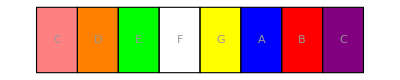

```mathematica
With[{toneRule={1->"C", 2->"D", 3->"E", 4->"F", 5->"G", 6->"A", 7->"B", 8->"C"},color={ Pink, Orange, Green, White,Yellow,Blue, Red, Purple}},
Graphics[Table[{EdgeForm[Directive[Thin,Black]],color[[i]],Rectangle[{i-1, 0}],GrayLevel[0.6], Style[Text[i/. toneRule, {i-.5,0.5}],FontSize->20]}, {i, 8}]]
]
```